# Dynamics of an Interaction between Pressure-less Dark Matter and a non-linear Dark Energy

## Vacuum Interaction

## Q = q1(x - ℛ)(1 - x)z

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z
de2:=y'=-y^2-(1/6)*(z-2*x)
de3:=z'=-3*y*z*(1-q1*(x-ℛ)*(1-x))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→2 x},{x→3 y^2,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y,z/.FPs[[2,2]]};
FP[3]={ℛ,Sqrt[ℛ/3],0};
FP[4]={ℛ,-Sqrt[ℛ/3],0};
FP[5]={ℛ,0,2*ℛ};
FP[6]={1,Sqrt[1/3],0};
FP[7]={1,-Sqrt[1/3],0};
FP[8]={1,0,2};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(3 q1 y z (-1+2 x-ℛ) | 3 q1 (-1+x) z (x-ℛ) | 3 q1 (-1+x) y (x-ℛ)
1/3 | -2 y | -1/6
-3 q1 y z (-1+2 x-ℛ) | 3 z (-1-q1 (-1+x) (x-ℛ)) | 3 y (-1-q1 (-1+x) (x-ℛ)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
2 x) | (0 | 6 q1 (-1+x) x (x-ℛ) | 0
1/3 | 0 | -1/6
0 | 6 x (-1-q1 (-1+x) (x-ℛ)) | 0) | (0
-√(x-3 q1 x^2+3 q1 x^3+3 q1 x ℛ-3 q1 x^2 ℛ)
√(x-3 q1 x^2+3 q1 x^3+3 q1 x ℛ-3 q1 x^2 ℛ)) | (1/2 | 0 | 1
-(-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)/(1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ) | (√(x (1-3 q1 x+3 q1 x^2+3 q1 ℛ-3 q1 x ℛ)))/(6 x (1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)) | 1
-(-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)/(1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ) | -(√(x (1-3 q1 x+3 q1 x^2+3 q1 ℛ-3 q1 x ℛ)))/(6 x (1-q1 x+q1 x^2+q1 ℛ-q1 x ℛ)) | 1)
(3 y^2
y
0) | (0 | 0 | 3 q1 y (-1+3 y^2) (3 y^2-ℛ)
1/3 | -2 y | -1/6
0 | 0 | 3 y (-1-q1 (-1+3 y^2) (3 y^2-ℛ))) | (0
-2 y
-3 y (1-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ)) | (6 y | 1 | 0
0 | 1 | 0
-(-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ)/(1-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ) | 1/(6 y (1-3 q1 y^2+9 q1 y^4+q1 ℛ-3 q1 y^2 ℛ)) | 1)
(ℛ
(√ℛ)/(√3)
0) | (0 | 0 | 0
1/3 | -(2 √ℛ)/(√3) | -1/6
0 | 0 | -√3 √ℛ) | (0
-√3 √ℛ
-(2 √ℛ)/(√3)) | (2 √3 √ℛ | 1 | 0
0 | 1/(2 √3 √ℛ) | 1
0 | 1 | 0)
(ℛ
-(√ℛ)/(√3)
0) | (0 | 0 | 0
1/3 | (2 √ℛ)/(√3) | -1/6
0 | 0 | √3 √ℛ) | (0
(2 √ℛ)/(√3)
√3 √ℛ) | (-2 √3 √ℛ | 1 | 0
0 | 1 | 0
0 | -1/(2 √3 √ℛ) | 1)
(ℛ
0
2 ℛ) | (0 | 0 | 0
1/3 | 0 | -1/6
0 | -6 ℛ | 0) | (0
-√ℛ
√ℛ) | (1/2 | 0 | 1
0 | 1/(6 √ℛ) | 1
0 | -1/(6 √ℛ) | 1)
(1
1/(√3)
0) | (0 | 0 | 0
1/3 | -2/(√3) | -1/6
0 | 0 | -√3) | (-√3
-2/(√3)
0) | (0 | 1/(2 √3) | 1
0 | 1 | 0
2 √3 | 1 | 0)
(1
-1/(√3)
0) | (0 | 0 | 0
1/3 | 2/(√3) | -1/6
0 | 0 | √3) | (√3
2/(√3)
0) | (0 | -1/(2 √3) | 1
0 | 1 | 0
-2 √3 | 1 | 0)
(1
0
2) | (0 | 0 | 0
1/3 | 0 | -1/6
0 | -6 | 0) | (-1
1
0) | (0 | 1/6 | 1
0 | -1/6 | 1
1/2 | 0 | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
Eqx[q1_,ℛ_]=de1;
Eqy=de2;
Eqz[q1_,ℛ_]=de3;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[PhaseSpace13D=StreamPlot3D[{Eqx[q1,ℛ],Eqy,Eqz[q1,ℛ]},{x,ℛ,1},{y,-1.5,1.5},{z,0,1.5},AxesLabel->{"x","y","z"}],{q1,4/(1-ℛ)^2,10,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"}]
```

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define z(x) and the first integral cz*)
α=0.5;

cz=(1/(q1*(1-ℛ))*Log[ℛ(1-α)/(α-ℛ)]-(ℛ/α)*(1+0.3111/0.6889))

z[x_,q1_,ℛ_]=(-q1)*x/q1+(1/(q1*(1-ℛ)))*Log[(x-ℛ)/(1-x)]-cz
```

-2.90318 ℛ+Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

```mathematica
Limit[z[x,q1,ℛ],x->ℛ]
```

(-∞)/(q1-1. q1 ℛ)

```mathematica
Limit[z[x,q1,ℛ],x->1]
```

Indeterminate

```mathematica
(*Left and right limits*)
```

```mathematica
Limit[z[x,q1,ℛ],x->ℛ,Direction->"FromAbove"]
```

(-∞)/(q1-1. q1 ℛ)

```mathematica
Limit[z[x,q1,ℛ],x->1,Direction->"FromBelow"]
```

(-∞)/(q1 (-1.+ℛ))

### Manipulate Plots

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q1*(x-ℛ)*(1-x)*z[x,q1,ℛ]
de2:=y'=-y^2-(1/6)*(z[x,q1,ℛ]-2*x)
de3:=z'=-3*y*z[x,q1,ℛ]*(1-q1*(x-ℛ)*(1-x))
```

```mathematica
Eqx[q1_,ℛ_,cz_]=de1;
Eqy[q1_,ℛ_,cz_]=de2;
Eqz[q1_,ℛ_,cz_]=de3;
```

-3 q1 (1-x) y (x-ℛ) (-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ)))

-y^2+1/6 (3 x-2.90318 ℛ-Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))+Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ)))

-3 y (1-q1 (1-x) (x-ℛ)) (-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ)))

```mathematica
xFP1[q1_,ℛ_]=(1/(2*(-q1)))*((-q1)*(1+ℛ)+Sqrt[(-q1)^2*(1-ℛ)^2+4*(-q1)])
```

-(√(-4 q1+q1^2 (1-ℛ)^2)-q1 (1+ℛ))/(2 q1)

```mathematica
z[x,q1,ℛ]
```

-x+2.90318 ℛ+Log[(x-ℛ)/(1-x)]/(q1 (1-ℛ))-Log[(0.5 ℛ)/(0.5-ℛ)]/(q1 (1-ℛ))

```mathematica
(*Plot to find the possible number of Einstein points*)
Plot[z[x,4,1,.1]-2*x,{x,.1,1}]
```

-Graphics-

```mathematica
Manipulate[PhaseSpacexy=StreamPlot[{Eqx[q1,ℛ,cz],Eqy[q1,ℛ,cz]},{x,ℛ,1},{y,-1,1},Epilog->{Inset[Text[Style[(1/(q1*(1-ℛ))*Log[ℛ(1-α)/(α-ℛ)]-(ℛ/α)*(1+0.3111/0.6889)),12]],{0.2,1}]}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}]

Manipulate[z0=ContourPlot[z[x,q1,ℛ]==0,{x,ℛ,1},{y,-1,1},ContourStyle->{Blue}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}]

Manipulate[Acc=ContourPlot[{2*x-z[x,q1,ℛ]==0},{x,ℛ,1},{y,-1,1},ContourStyle->{Red, Thick}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}]

Manipulate[Decn=ContourPlot[{2*x-z[x,q1,ℛ]==-.1},{x,ℛ,1},{y,-1,1},ContourStyle->{Magenta, Thick}],{q1,4/(1-ℛ)^2,20,Appearance->"Open"},{ℛ,0,0.2,Appearance->"Open"}];

Show[PhaseSpacexy,z0,Acc]//Dynamic
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(*Plot of the range of x values for a dS fixed point*)
xdS1[ℛ_,q1_]=(1+ℛ)/2+Sqrt[(1-ℛ)^2/4-1/q1];
xdS2[ℛ_,q1_]=(1+ℛ)/2-Sqrt[(1-ℛ)^2/4-1/q1];

Manipulate[Plot[{xdS1[ℛ,q1],xdS2[ℛ,q1]},{q1,4/(1-ℛ)^2,100},PlotStyle->{Blue,Red},GridLines->{{4/(1-ℛ)^2},{ℛ,1}},GridLinesStyle->Directive[Black,Thick,Dashed],AxesLabel->{"q1","x(Fixed Point)"}],{ℛ,0,1,Appearance->"Open"}]
```

### Numeric Integration

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
ℛ=0.01
```

0.01

```mathematica
de1t:=x'[t]==-3*y[t]*q1*(x[t]-ℛ)*(1-x[t])*((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)
de2t:=y'[t]==-y[t]^2-(1/6)*(((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)-2*x[t])
de3t:=z'[t]==-3*y[t]*((-q1)*x[t]/q1+(1/(q1*(1-ℛ)))*Log[(x[t]-ℛ)/(1-x[t])]-cz)*(1-q1*(x[t]-ℛ)*(1-x[t]))
```

```mathematica
(*The remaining equation when y' = y = 0, which can be solved to find the number of Einstein points admitted by the system*)
f[x_,q1_,ℛ_]=z[x,q1,ℛ]-2*x
```

0.0290318+4.63128/q1-3 x+(1.0101 Log[(-0.01+x)/(1-x)])/q1

```mathematica
(*Find the limit of f when x -> ℛ*)
Limit[f[x,q1,ℛ],x->ℛ, Assumptions->{q1>4/((1-ℛ)^2),0<ℛ<1}]
```

-∞

```mathematica
(*Find the limit of f when x -> 1*)
Limit[f[x,q1,ℛ],x->1, Assumptions->{q1>4/((1-ℛ)^2),0<ℛ<1}]
```

∞

```mathematica
(*Find derivative of f(x) with respect to x*)
fDeriv[x_,q1_,ℛ_]=Simplify[D[f[x,q1,ℛ],x]]
```

(-1.+q1 (-0.03+3.03 x-3. x^2))/(q1 (-1.+x) (-0.01+x))

```mathematica
(*Solve f'(x)=0 for q1 in limiting case*)
q1Lim[x_,ℛ_]=Solve[fDeriv[x,q1,ℛ]==0,q1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q1→-33.3333/(1.-101. x+100. x^2)}}

```mathematica
q1Lim[x_,ℛ_]=q1/.q1Lim[x,ℛ]
```

{-33.3333/(1.-101. x+100. x^2)}

```mathematica
ℛ=0.01;
```

0.01

## Plots

### No Einstein Points

```mathematica
(*Define the interaction constant value for this case*)
q1=15;
```

```mathematica
cz
```

```mathematica
(*Define the equation for the FFS from the Friedmann equation*)
FFS=Sqrt[x/3+z[x,q1,ℛ]/3];
```

```mathematica
(*Plot the FFS*)
FFS0EPts = Plot[{FFS,-FFS},{x,ℛ,1} ,PlotStyle -> {Black, Thick}];
```

```mathematica
(*Plot trajectories with different initial conditions*)
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.1}, {x,y},{t,-20,20}]; 
Traj2 = NDSolve[{de1t,de2t, y[0]== .1, x[0]== .99}, {x,y},{t,-20,20}]; 
Traj3 = NDSolve[{de1t,de2t, y[0]== 0.1, x[0]==0.2}, {x,y},{t,-20,20}]; 
Traj0EPts = ParametricPlot[Evaluate[{x[t],y[t]}/.{ Traj1,Traj2,Traj3},{t,-20,20}, PlotStyle -> {{Gray, Opacity[0.75]}}]];


(*Plot*)
(*Show[FFS0EPts,Traj0EPts]*)
```

### 2 Einstein Points

```mathematica
(*Define the interaction constant value for this case*)
q1=7;
```

```mathematica
cz
```

```mathematica
(*Substitute q1Lim into f(x)=0 and solve for x*)
x1=x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.1}]

x2=x/.FindRoot[f[x,q1Lim[x,ℛ],ℛ]==0,{x,0.7}]
```

0.0378015

0.841311

```mathematica
(*Find corresponding q1 values*)
q1Lim1=q1Lim[x1,ℛ]
q1Lim2=q1Lim[x2,ℛ]
```

{12.4608}

{2.52678}

```mathematica
xTwoEinsteinPointsq1i=FindRoot[f[x,q1,ℛ]==0,{x,0.025}]
xTwoEinsteinPointsq1ii=FindRoot[f[x,q1,ℛ]==0,{x,0.13}]
xTwoEinsteinPointsq1iii=FindRoot[f[x,q1,ℛ]==0,{x,0.9999998}]
```

{x→0.0232042}

{x→0.138837}

{x→1.}

```mathematica
0.999999889017173
```

1.

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsq1={x/.xTwoEinsteinPointsq1i,x/.xTwoEinsteinPointsq1ii,x/.xTwoEinsteinPointsq1iii}
```

{0.0232042,0.138837,1.}

```mathematica
(*Calculate the z values of the Einstein points*)
zTwoEinsteinPointsq1=z[xTwoEinsteinPointsq1,q1,ℛ]
```

{0.0464084,0.277674,2.}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[1]={xTwoEinsteinPointsq1[[1]],0,zTwoEinsteinPointsq1[[1]]}
EinsteinFP[2]={xTwoEinsteinPointsq1[[2]],0,zTwoEinsteinPointsq1[[2]]}
EinsteinFP[3]={xTwoEinsteinPointsq1[[3]],0,zTwoEinsteinPointsq1[[3]]}
```

{0.0232042,0,0.0464084}

{0.138837,0,0.277674}

{1.,0,2.}

```mathematica
(*Define the equation for the FFS from the Friedmann equation*)
FFS=Sqrt[(1/3)*(x+z[x,q1,ℛ])];
```

```mathematica
(*FFS reaches y = 0 at x > ℛ*)
Solve[x/3+z[x,q1,ℛ]/3==0]
```

{{x→0.0181926}}

```mathematica
(*Plot the FFS*)
FFS2EPts = Plot[{FFS,-FFS},{x,ℛ,1} ,PlotStyle -> {{Darker[Green], Thick}}];
```

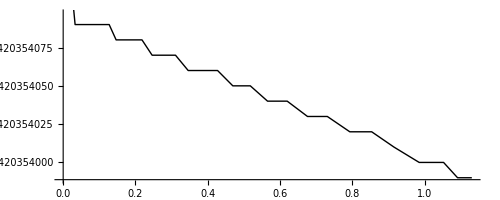

```mathematica
(*Plot the CFS*)
CFS2EPts=NDSolve[{de1t,de2t, y[0]== 0.00001, x[0]==0.023204203540973366}, {x,y},{t,-20,20}];

CFS2EPts=ParametricPlot[Evaluate[{y[t],x[t]}/.{CFS2EPts}, {t,-20,20}, PlotStyle -> {{Black, Thick}}]]
```

```mathematica
(*Plot the fixed points*)
FPShow2EPts=ListPlot[{{xTwoEinsteinPointsq1[[1]],0},{xTwoEinsteinPointsq1[[2]],0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
FindRoot[z[x,q1,ℛ]-2*x==0,{x,0.02}]
```

{x→0.0232042}

```mathematica
(z[x,q1,ℛ]-2*x)/.{x->0.023204203540973366}
```

-4.59632×10^-14

```mathematica
(*Plot the boundary between accelerating and decelerating region*)
(*Could create Table with values of x between ℛ and 1 with small step size*)
Acc2EPts1=ContourPlot[{f[x,q1,ℛ]==0},{x,0.1,0.2} ,{y,-1,1},ContourStyle->{Red, Thick}];

Acc2EPts2=ContourPlot[{f[x,q1,ℛ]==0},{x,0.02,0.03},{y,-1,1},ContourStyle->{Red, Thick}];
```

```mathematica
(*Set up plot for x = ℛ and x = 1 separatrices*)
Sepx=ContourPlot[{x==ℛ,x==1},{x,0,1.1},{y,-1,1},ContourStyle->{{Black,Thick}},PlotRange->Full];
```

```mathematica
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.45}, {x,y},{t,-40,40}];
```

```mathematica
(*Plot trajectories with different initial conditions*)
Traj1 = NDSolve[{de1t,de2t, y[0]==0.1, x[0]==.2}, {x,y},{t,-40,40}]; 
Traj2 = NDSolve[{de1t,de2t, y[0]== -0.2, x[0]== .9}, {x,y},{t,-40,40}]; 
Traj3 = NDSolve[{de1t,de2t, y[0]==0.5, x[0]==0.011}, {x,y},{t,-40,40}]; 

Traj2EPts = ParametricPlot[Evaluate[{x[t],y[t]}/.{ Traj1,Traj2,Traj3}, {t,-40,40}, PlotStyle -> {{Gray, Opacity[0.75]}}]];
```

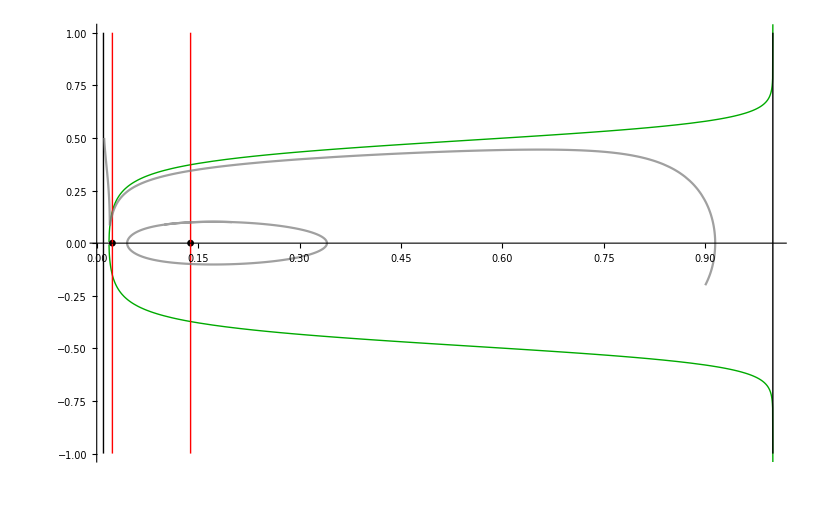

```mathematica
(*Plot all components of the phase space*)
Show[FFS2EPts,FPShow2EPts,Acc2EPts1, Acc2EPts2,Sepx,Traj2EPts,PlotRange->{{ℛ,1},{-1,1}}]
```

```mathematica
FPShow2EPts3D=ListPointPlot3D[{{xTwoEinsteinPointsq1[[1]],0,z[xTwoEinsteinPointsq1[[1]],q1,ℛ]},{xTwoEinsteinPointsq1[[2]],0,z[xTwoEinsteinPointsq1[[2]],q1,ℛ]},{xTwoEinsteinPointsq1[[3]],0,z[xTwoEinsteinPointsq1[[3]],q1,ℛ]},{ℛ,Sqrt[ℛ/3],z[ℛ,q1,ℛ]},{ℛ,-Sqrt[ℛ/3],z[ℛ,q1,ℛ]},{1,Sqrt[1/3],z[1,q1,ℛ]},{1,-Sqrt[1/3],z[1,q1,ℛ]}},PlotStyle->{Black}]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics3D-

```mathematica
Accn3D=ContourPlot3D[(1/6)*(2*x-z)==0,{x,ℛ,1},{y,-1,1},{z,0,2.2}, ContourStyle->{Red,Opacity[0.3], Thick}]
```

-Graphics3D-

```mathematica
Dcn3D=ContourPlot3D[(1/6)*(2*x-z)==-0.1,{x,ℛ,1},{y,-1,1},{z,0,2.2}, ContourStyle->{Red,Opacity[0.3], Thick}];
```

```mathematica
(*Accn3D=Plot3D[(1/6)*(2*x-z[x,q1,ℛ]),{x,ℛ,1},{y,-1,1},PlotStyle -> {Red, Opacity[0.25]},Mesh->False,PlotPoints->100]*)
```

```mathematica
Acc=ContourPlot3D[f[x,q1,ℛ]==0,{x,ℛ,1},{y,-1,1},{z,0,2.2}]
```

-Graphics3D-

```mathematica
Surface=ParametricPlot3D[{x,y,z[x,q1,ℛ]},{x,ℛ,1},{y,-1,1},PlotStyle -> {{Yellow, Opacity[0.4]}},AxesLabel->{"x","y","z"},Mesh->None,PlotRange->{{0.01,1},{-1,1},{0,1}}]
```

-Graphics3D-

```mathematica
(*FFS*)
FFS3D=ParametricPlot3D[{{x,Sqrt[(1/3)*(x+z)],z},{x,-Sqrt[(1/3)*(x+z)],z}},{x,ℛ,1},{z,0,2.2},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008],Opacity[0.2]}}]
```

-Graphics3D-

```mathematica
Show[Accn3D,Acc,Surface,FPShow2EPts3D,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Q = q(x - ℛ)(1 - x)

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q*(x-ℛ)*(1-x)
de2:=y'=-y^2-(1/6)*(z-2*x)
de3:=z'=-3*y*z+q*(x-ℛ)*(1-x)*y
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→2 x},{x→1,y→-1/(√3),z→0},{x→1,y→1/(√3),z→0},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(3 q y (-1+2 x-ℛ) | 3 q (-1+x) (x-ℛ) | 0
1/3 | -2 y | -1/6
q y (1-2 x+ℛ) | -3 z-q (-1+x) (x-ℛ) | -3 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
2 x) | (0 | 3 q (-1+x) (x-ℛ) | 0
1/3 | 0 | -1/6
0 | -6 x-q (-1+x) (x-ℛ) | 0) | (0
-(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6)
(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6)) | (1/2 | 0 | 1
-(3 (-q x+q x^2+q ℛ-q x ℛ))/(6 x-q x+q x^2+q ℛ-q x ℛ) | (√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6 (6 x-q x+q x^2+q ℛ-q x ℛ)) | 1
-(3 (-q x+q x^2+q ℛ-q x ℛ))/(6 x-q x+q x^2+q ℛ-q x ℛ) | -(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6 (6 x-q x+q x^2+q ℛ-q x ℛ)) | 1)
(1
-1/(√3)
0) | (√3 q (-1+ℛ) | 0 | 0
1/3 | 2/(√3) | -1/6
-(q (-1+ℛ))/(√3) | 0 | √3) | (√3
2/(√3)
√3 q (-1+ℛ)) | (0 | -1/(2 √3) | 1
0 | 1 | 0
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | -(-6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) (-2-3 q+3 q ℛ)) | 1)
(1
1/(√3)
0) | (-√3 q (-1+ℛ) | 0 | 0
1/3 | -2/(√3) | -1/6
(q (-1+ℛ))/(√3) | 0 | -√3) | (-√3
-2/(√3)
-√3 q (-1+ℛ)) | (0 | 1/(2 √3) | 1
0 | 1 | 0
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | (-6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) (-2-3 q+3 q ℛ)) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (-√3 q (-1+ℛ) √ℛ | 0 | 0
1/3 | (2 √ℛ)/(√3) | -1/6
(q (-1+ℛ) √ℛ)/(√3) | 0 | √3 √ℛ) | ((2 √ℛ)/(√3)
√3 √ℛ
-√3 q (-1+ℛ) √ℛ) | (0 | 1 | 0
0 | -1/(2 √3 √ℛ) | 1
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | (6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) √ℛ (2-3 q+3 q ℛ)) | 1)
(ℛ
(√ℛ)/(√3)
0) | (√3 q (-1+ℛ) √ℛ | 0 | 0
1/3 | -(2 √ℛ)/(√3) | -1/6
-(q (-1+ℛ) √ℛ)/(√3) | 0 | -√3 √ℛ) | (-√3 √ℛ
-(2 √ℛ)/(√3)
√3 q (-1+ℛ) √ℛ) | (0 | 1/(2 √3 √ℛ) | 1
0 | 1 | 0
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | -(6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) √ℛ (2-3 q+3 q ℛ)) | 1)

```mathematica
Eq1[q_,ℛ_]=de1;
Eq2[ℛ_]=de2;
Eq3[q_,ℛ_]=de3;
```

-3 q (1-x) y (x-ℛ)

-y^2+1/6 (2 x-z)

-3 y z+q (1-x) y (x-ℛ)

```mathematica
Manipulate[StreamPlot3D[{Eq1[q,ℛ],Eq2[ℛ],Eq3[q,ℛ]},{x,0,1},{y,-1,1},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,5,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4342'[System`VectorPlotsDump`t$4342]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4342[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4342'[System`VectorPlotsDump`t$4342]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4342[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4342,System`VectorPlotsDump`linesxmax$4342},{System`VectorPlotsDump`linesymin$4342,System`VectorPlotsDump`linesymax$4342},{System`VectorPlotsDump`lineszmin$4342,«37»},{System`VectorPlotsDump`linesfieldmin$4342,System`VectorPlotsDump`linesfieldmax$4342}} and System`VectorPlotsDump`extremes$4438 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4342'[System`VectorPlotsDump`t$4342]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4342[0]=={0.1,-0.8,«19»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4342'[System`VectorPlotsDump`t$4342]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4342[0]=={0.1,-0.8,«19»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4342,System`VectorPlotsDump`linesxmax$4342},{System`VectorPlotsDump`linesymin$4342,System`VectorPlotsDump`linesymax$4342},{System`VectorPlotsDump`lineszmin$4342,«37»},{System`VectorPlotsDump`linesfieldmin$4342,System`VectorPlotsDump`linesfieldmax$4342}} and System`VectorPlotsDump`extremes$4524 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4342'[System`VectorPlotsDump`t$4342]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4342[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«4»] and NDSolveValue[{System`VectorPlotsDump`w$4342'[System`VectorPlotsDump`t$4342]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4342[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«4»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4342,System`VectorPlotsDump`linesxmax$4342},{System`VectorPlotsDump`linesymin$4342,System`VectorPlotsDump`linesymax$4342},{System`VectorPlotsDump`lineszmin$4342,«37»},{System`VectorPlotsDump`linesfieldmin$4342,System`VectorPlotsDump`linesfieldmax$4342}} and System`VectorPlotsDump`extremes$4598 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7214'[System`VectorPlotsDump`t$7214]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7214[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$7214'[System`VectorPlotsDump`t$7214]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7214[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7214,System`VectorPlotsDump`linesxmax$7214},{System`VectorPlotsDump`linesymin$7214,System`VectorPlotsDump`linesymax$7214},{System`VectorPlotsDump`lineszmin$7214,«37»},{System`VectorPlotsDump`linesfieldmin$7214,System`VectorPlotsDump`linesfieldmax$7214}} and System`VectorPlotsDump`extremes$7271 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7214'[System`VectorPlotsDump`t$7214]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7214[0]=={0.1,-0.8,«19»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$7214'[System`VectorPlotsDump`t$7214]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7214[0]=={0.1,-0.8,«19»,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7214,System`VectorPlotsDump`linesxmax$7214},{System`VectorPlotsDump`linesymin$7214,System`VectorPlotsDump`linesymax$7214},{System`VectorPlotsDump`lineszmin$7214,«37»},{System`VectorPlotsDump`linesfieldmin$7214,System`VectorPlotsDump`linesfieldmax$7214}} and System`VectorPlotsDump`extremes$7339 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7214'[System`VectorPlotsDump`t$7214]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7214[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«4»] and NDSolveValue[{System`VectorPlotsDump`w$7214'[System`VectorPlotsDump`t$7214]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7214[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«4»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7214,System`VectorPlotsDump`linesxmax$7214},{System`VectorPlotsDump`linesymin$7214,System`VectorPlotsDump`linesymax$7214},{System`VectorPlotsDump`lineszmin$7214,«37»},{System`VectorPlotsDump`linesfieldmin$7214,System`VectorPlotsDump`linesfieldmax$7214}} and System`VectorPlotsDump`extremes$7417 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$32045'[System`VectorPlotsDump`t$32045]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$32045[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,«1»] and NDSolveValue[{System`VectorPlotsDump`w$32045'[System`VectorPlotsDump`t$32045]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$32045[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$32045,System`VectorPlotsDump`linesxmax$32045},{System`VectorPlotsDump`linesymin$32045,System`VectorPlotsDump`linesymax$32045},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$32045,System`VectorPlotsDump`linesfieldmax$32045}} and System`VectorPlotsDump`extremes$32094 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$32045'[System`VectorPlotsDump`t$32045]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$32045[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,«1»] and NDSolveValue[{System`VectorPlotsDump`w$32045'[System`VectorPlotsDump`t$32045]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$32045[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$32045,System`VectorPlotsDump`linesxmax$32045},{System`VectorPlotsDump`linesymin$32045,System`VectorPlotsDump`linesymax$32045},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$32045,System`VectorPlotsDump`linesfieldmax$32045}} and System`VectorPlotsDump`extremes$32149 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$32045'[System`VectorPlotsDump`t$32045]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$32045[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,«1»] and NDSolveValue[{System`VectorPlotsDump`w$32045'[System`VectorPlotsDump`t$32045]=={Eq1[0.01,0.1],Eq2[0.1],Eq3[0.01,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$32045[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$32045,System`VectorPlotsDump`linesxmax$32045},{System`VectorPlotsDump`linesymin$32045,System`VectorPlotsDump`linesymax$32045},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$32045,System`VectorPlotsDump`linesfieldmax$32045}} and System`VectorPlotsDump`extremes$32210 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*System of differential equations for x and z -> time variable is lna*)
dex:=x'=-3*q*(x-ℛ)*(1-x)
dez:=z'=-3*z+q*(x-ℛ)*(1-x)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→1,z→0},{x→ℛ,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(3 q (-1+2 x-ℛ) | 0
q (1-2 x+ℛ) | -3)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(1
0) | (-3 q (-1+ℛ) | 0
q (-1+ℛ) | -3) | (-3
-3 q (-1+ℛ)) | (0 | 1
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | 1)
(ℛ
0) | (3 q (-1+ℛ) | 0
q-q ℛ | -3) | (-3
3 q (-1+ℛ)) | (0 | 1
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | 1)

```mathematica
Eqx[q_,ℛ_]=dex;
Eqz[q_,ℛ_]=dez;
```

```mathematica
Manipulate[StreamPlot[{Eqz[q,ℛ],Eqx[q,ℛ]},{z,-.2,1},{x,ℛ,1},FrameLabel->{"z","x"}],{q,0,1,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

### Compact Phase Plot

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
de1t:=x'[t]==-3*Y[t]*q*(x[t]-ℛ)*(1-x[t])/((1-Y[t]^2)^(1/2))
de2t:=Y'[t]==-(Y[t]^2)*(1-Y[t]^2)^(1/2)-(((1-Y[t]^2)^(3/2))/6)*((Z[t]/(1-Z[t]))-2*x[t])
de3t:=Z'[t]==-3*Y[t]*Z[t]*(1-Z[t])/((1-Y[t]^2)^(1/2))+q*(1-Z[t])^2*(x[t]-ℛ)*(1-x[t])*Y[t]/((1-Y[t]^2)^(1/2))
```

```mathematica
dext:=x'[t]==-3*q*(x[t]-ℛ)*(1-x[t])
dezt:=z'[t]==-3*z[t]+q*(x[t]-ℛ)*(1-x[t])
```

```mathematica
q=0.01;
ℛ=0.01;
```

```mathematica
traj[x0_,Y0_,Z0_]=NDSolve[{de1t,de2t,de3t, x[0]==x0,Y[0]==Y0,Z[0]==Z0}, {x,Y,Z},{t,-500,500}];
```

```mathematica
sol[1]=traj[0.02,0.01,0.009];
sol[2]=traj[0.02,0.05,0.009];
sol[3]=traj[0.8,0.055,0.009];
sol[4]=traj[0.99,0.06,0.009];
sol[5]=traj[0.02,0.08,0.009];
sol[6]=traj[0.02,0.09,0.009];
```

Power::infy: Infinite expression 1/(√0.) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {ComplexInfinity,Indeterminate,Indeterminate} is not a list of numbers with dimensions {3} at {t,x[t],Y[t],Z[t]} = {-29.1365,0.0824078,1.,1.}.

Power::infy: Infinite expression 1/(√0.) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {ComplexInfinity,Indeterminate,Indeterminate} is not a list of numbers with dimensions {3} at {t,x[t],Y[t],Z[t]} = {-12.1624,0.993153,1.,1.}.

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {-15688.1,ComplexInfinity,0.} is not a list of numbers with dimensions {3} at {t,x[t],Y[t],Z[t]} = {-10.6332,0.992065,1.,1.}.

InterpolatingFunction::dmval: Input value {-499.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

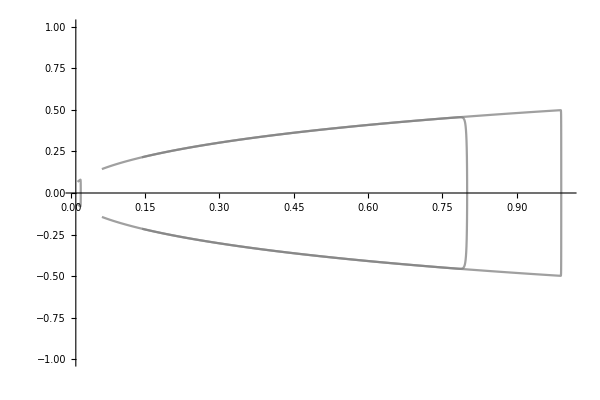

```mathematica
ParametricPlot[Evaluate[Table[{x[t],Y[t]}/.sol[i],{i,1,6}], {t,-500,500},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,400},PlotRange->{{ℛ,1},{-1,1}}]]
```

## Generic Dark Energy with Interaction Term

## Ecological Models: Case 1

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z), Hubble parameter (y) and dark energy (x)*)
dex3D:=x'=-3*y*(x-ℛ)*(1-x)-q*z*x*y
dey3D:=y'=-y^2-(1/6)*(x*(1+3*ℛ)-3*ℛ-3*x^2+z)
dez3D:=z'=-3*z *y+ q*x*z*y
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex3D==0,dey3D==0,dez3D==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x+3 x^2+3 ℛ-3 x ℛ},{x→1,y→-1/(√3),z→0},{x→1,y→1/(√3),z→0},{x→3/q,y→-(√(9-3 q ℛ+q^2 ℛ))/(√3 q),z→((-3+q) (-3+q ℛ))/q^2},{x→3/q,y→(√(9-3 q ℛ+q^2 ℛ))/(√3 q),z→((-3+q) (-3+q ℛ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex3D,x],D[dex3D,y],D[dex3D,z]}, {D[dey3D,x],D[dey3D,y],D[dey3D,z]},{D[dez3D,x],D[dez3D,y],D[dez3D,z]}}];
J//MatrixForm
```

(y (6 x-q z-3 (1+ℛ)) | -q x z+3 (-1+x) (x-ℛ) | -q x y
-1/6+x-ℛ/2 | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x+3 x^2+3 ℛ-3 x ℛ) | (0 | -3 q x^3+3 ℛ-3 x (1+ℛ+q ℛ)+x^2 (3+q+3 q ℛ) | 0
-1/6+x-ℛ/2 | 0 | -1/6
0 | (-3+q x) (3 x^2+3 ℛ-x (1+3 ℛ)) | 0) | (0
-(√(-4 x^2+6 x^3+2 q x^3-6 q x^4+2 ℛ+7 x ℛ-9 x^2 ℛ-7 q x^2 ℛ+9 q x^3 ℛ-3 ℛ^2+3 x ℛ^2+3 q x ℛ^2-3 q x^2 ℛ^2))/(√2)
(√(-4 x^2+6 x^3+2 q x^3-6 q x^4+2 ℛ+7 x ℛ-9 x^2 ℛ-7 q x^2 ℛ+9 q x^3 ℛ-3 ℛ^2+3 x ℛ^2+3 q x ℛ^2-3 q x^2 ℛ^2))/(√2)) | (-1/(1-6 x+3 ℛ) | 0 | 1
-(3 x-3 x^2-q x^2+3 q x^3-3 ℛ+3 x ℛ+3 q x ℛ-3 q x^2 ℛ)/((-3+q x) (-x+3 x^2+3 ℛ-3 x ℛ)) | -(√(-4 x^2+6 x^3+2 q x^3-6 q x^4+2 ℛ+7 x ℛ-9 x^2 ℛ-7 q x^2 ℛ+9 q x^3 ℛ-3 ℛ^2+3 x ℛ^2+3 q x ℛ^2-3 q x^2 ℛ^2))/(√2 (-3+q x) (-x+3 x^2+3 ℛ-3 x ℛ)) | 1
-(3 x-3 x^2-q x^2+3 q x^3-3 ℛ+3 x ℛ+3 q x ℛ-3 q x^2 ℛ)/((-3+q x) (-x+3 x^2+3 ℛ-3 x ℛ)) | (√(-4 x^2+6 x^3+2 q x^3-6 q x^4+2 ℛ+7 x ℛ-9 x^2 ℛ-7 q x^2 ℛ+9 q x^3 ℛ-3 ℛ^2+3 x ℛ^2+3 q x ℛ^2-3 q x^2 ℛ^2))/(√2 (-3+q x) (-x+3 x^2+3 ℛ-3 x ℛ)) | 1)
(1
-1/(√3)
0) | (√3 (-1+ℛ) | 0 | q/(√3)
1/6 (5-3 ℛ) | 2/(√3) | -1/6
0 | 0 | -(-3+q)/(√3)) | (2/(√3)
-(-3+q)/(√3)
√3 (-1+ℛ)) | (0 | 1 | 0
-q/(-6+q+3 ℛ) | -(√3 (-2+ℛ))/(2 (-6+q+3 ℛ)) | 1
-2 √3 | 1 | 0)
(1
1/(√3)
0) | (-√3 (-1+ℛ) | 0 | -q/(√3)
1/6 (5-3 ℛ) | -2/(√3) | -1/6
0 | 0 | (-3+q)/(√3)) | (-2/(√3)
(-3+q)/(√3)
-√3 (-1+ℛ)) | (0 | 1 | 0
-q/(-6+q+3 ℛ) | (√3 (-2+ℛ))/(2 (-6+q+3 ℛ)) | 1
2 √3 | 1 | 0)
(3/q
-(√(9-3 q ℛ+q^2 ℛ))/(√3 q)
((-3+q) (-3+q ℛ))/q^2) | ((√(3-q ℛ+(q^2 ℛ)/3) (-9+q^2 ℛ))/q^2 | 0 | (√3 √(9-3 q ℛ+q^2 ℛ))/q
-1/6+3/q-ℛ/2 | (2 √(3-q ℛ+(q^2 ℛ)/3))/q | -1/6
-((-3+q) (-3+q ℛ) √(3-q ℛ+(q^2 ℛ)/3))/q^2 | 0 | 0) | ((2 √(9-3 q ℛ+q^2 ℛ))/(√3 q)
(-18 √3 √(9-3 q ℛ+q^2 ℛ)+2 √3 q^2 ℛ √(9-3 q ℛ+q^2 ℛ)-√(8748-11664 q+3888 q^2-2916 q ℛ+6804 q^2 ℛ-3888 q^3 ℛ+432 q^4 ℛ-648 q^3 ℛ^2+756 q^4 ℛ^2-144 q^5 ℛ^2-36 q^5 ℛ^3+12 q^6 ℛ^3))/(12 q^2)
(-18 √3 √(9-3 q ℛ+q^2 ℛ)+2 √3 q^2 ℛ √(9-3 q ℛ+q^2 ℛ)+√(8748-11664 q+3888 q^2-2916 q ℛ+6804 q^2 ℛ-3888 q^3 ℛ+432 q^4 ℛ-648 q^3 ℛ^2+756 q^4 ℛ^2-144 q^5 ℛ^2-36 q^5 ℛ^3+12 q^6 ℛ^3))/(12 q^2)) | (0 | 1 | 0
(3 (-81-36 q+27 q ℛ+12 q^2 ℛ-4 q^3 ℛ-3 q^3 ℛ^2+q^4 ℛ^2-√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))))/(2 (-324+81 q+189 q ℛ-81 q^2 ℛ+9 q^3 ℛ-27 q^2 ℛ^2+15 q^3 ℛ^2-2 q^4 ℛ^2+√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))) | -(99 q^2 √(9-3 q ℛ+q^2 ℛ)-6 q^3 √(9-3 q ℛ+q^2 ℛ)-18 q^3 ℛ √(9-3 q ℛ+q^2 ℛ)+q^4 ℛ √(9-3 q ℛ+q^2 ℛ)+q^2 √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))/(81 √3 (9-3 q ℛ+q^2 ℛ)+36 √3 q (9-3 q ℛ+q^2 ℛ)-18 √3 q^2 ℛ (9-3 q ℛ+q^2 ℛ)-4 √3 q^3 ℛ (9-3 q ℛ+q^2 ℛ)+√3 q^4 ℛ^2 (9-3 q ℛ+q^2 ℛ)-√3 (9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)-4 √3 q √(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))) | 1
-(3 (-81-36 q+27 q ℛ+12 q^2 ℛ-4 q^3 ℛ-3 q^3 ℛ^2+q^4 ℛ^2+√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))))/(2 (324-81 q-189 q ℛ+81 q^2 ℛ-9 q^3 ℛ+27 q^2 ℛ^2-15 q^3 ℛ^2+2 q^4 ℛ^2+√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))) | -(99 q^2 √(9-3 q ℛ+q^2 ℛ)-6 q^3 √(9-3 q ℛ+q^2 ℛ)-18 q^3 ℛ √(9-3 q ℛ+q^2 ℛ)+q^4 ℛ √(9-3 q ℛ+q^2 ℛ)-q^2 √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))/(81 √3 (9-3 q ℛ+q^2 ℛ)+36 √3 q (9-3 q ℛ+q^2 ℛ)-18 √3 q^2 ℛ (9-3 q ℛ+q^2 ℛ)-4 √3 q^3 ℛ (9-3 q ℛ+q^2 ℛ)+√3 q^4 ℛ^2 (9-3 q ℛ+q^2 ℛ)-√3 (9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)+4 √3 q √(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))) | 1)
(3/q
(√(9-3 q ℛ+q^2 ℛ))/(√3 q)
((-3+q) (-3+q ℛ))/q^2) | (((9-q^2 ℛ) √(3-q ℛ+(q^2 ℛ)/3))/q^2 | 0 | -(√3 √(9-3 q ℛ+q^2 ℛ))/q
-1/6+3/q-ℛ/2 | -(2 √(3-q ℛ+(q^2 ℛ)/3))/q | -1/6
((-3+q) (-3+q ℛ) √(3-q ℛ+(q^2 ℛ)/3))/q^2 | 0 | 0) | (-(2 √(9-3 q ℛ+q^2 ℛ))/(√3 q)
(18 √3 √(9-3 q ℛ+q^2 ℛ)-2 √3 q^2 ℛ √(9-3 q ℛ+q^2 ℛ)-√(8748-11664 q+3888 q^2-2916 q ℛ+6804 q^2 ℛ-3888 q^3 ℛ+432 q^4 ℛ-648 q^3 ℛ^2+756 q^4 ℛ^2-144 q^5 ℛ^2-36 q^5 ℛ^3+12 q^6 ℛ^3))/(12 q^2)
(18 √3 √(9-3 q ℛ+q^2 ℛ)-2 √3 q^2 ℛ √(9-3 q ℛ+q^2 ℛ)+√(8748-11664 q+3888 q^2-2916 q ℛ+6804 q^2 ℛ-3888 q^3 ℛ+432 q^4 ℛ-648 q^3 ℛ^2+756 q^4 ℛ^2-144 q^5 ℛ^2-36 q^5 ℛ^3+12 q^6 ℛ^3))/(12 q^2)) | (0 | 1 | 0
-(3 (-81-36 q+27 q ℛ+12 q^2 ℛ-4 q^3 ℛ-3 q^3 ℛ^2+q^4 ℛ^2+√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))))/(2 (324-81 q-189 q ℛ+81 q^2 ℛ-9 q^3 ℛ+27 q^2 ℛ^2-15 q^3 ℛ^2+2 q^4 ℛ^2+√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))) | -(-99 q^2 √(9-3 q ℛ+q^2 ℛ)+6 q^3 √(9-3 q ℛ+q^2 ℛ)+18 q^3 ℛ √(9-3 q ℛ+q^2 ℛ)-q^4 ℛ √(9-3 q ℛ+q^2 ℛ)+q^2 √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))/(81 √3 (9-3 q ℛ+q^2 ℛ)+36 √3 q (9-3 q ℛ+q^2 ℛ)-18 √3 q^2 ℛ (9-3 q ℛ+q^2 ℛ)-4 √3 q^3 ℛ (9-3 q ℛ+q^2 ℛ)+√3 q^4 ℛ^2 (9-3 q ℛ+q^2 ℛ)-√3 (9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)+4 √3 q √(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))) | 1
(3 (-81-36 q+27 q ℛ+12 q^2 ℛ-4 q^3 ℛ-3 q^3 ℛ^2+q^4 ℛ^2-√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))))/(2 (-324+81 q+189 q ℛ-81 q^2 ℛ+9 q^3 ℛ-27 q^2 ℛ^2+15 q^3 ℛ^2-2 q^4 ℛ^2+√(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))) | -(-99 q^2 √(9-3 q ℛ+q^2 ℛ)+6 q^3 √(9-3 q ℛ+q^2 ℛ)+18 q^3 ℛ √(9-3 q ℛ+q^2 ℛ)-q^4 ℛ √(9-3 q ℛ+q^2 ℛ)-q^2 √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)))/(81 √3 (9-3 q ℛ+q^2 ℛ)+36 √3 q (9-3 q ℛ+q^2 ℛ)-18 √3 q^2 ℛ (9-3 q ℛ+q^2 ℛ)-4 √3 q^3 ℛ (9-3 q ℛ+q^2 ℛ)+√3 q^4 ℛ^2 (9-3 q ℛ+q^2 ℛ)-√3 (9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ)-4 √3 q √(9-3 q ℛ+q^2 ℛ) √((9-6 q+q^2 ℛ)^2 (9-3 q ℛ+q^2 ℛ))) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (-√3 (-1+ℛ) √ℛ | 0 | (q ℛ^(3/2))/(√3)
1/6 (-1+3 ℛ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (3-q ℛ))/(√3)) | ((2 √ℛ)/(√3)
-√3 (-1+ℛ) √ℛ
-(√ℛ (-3+q ℛ))/(√3)) | (0 | 1 | 0
-2 √3 √ℛ | 1 | 0
-q/(-3+q) | (√3)/(2 (-3+q) √ℛ) | 1)
(ℛ
(√ℛ)/(√3)
0) | (√3 (-1+ℛ) √ℛ | 0 | -(q ℛ^(3/2))/(√3)
1/6 (-1+3 ℛ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (-3+q ℛ))/(√3)) | (-(2 √ℛ)/(√3)
√3 (-1+ℛ) √ℛ
(√ℛ (-3+q ℛ))/(√3)) | (0 | 1 | 0
2 √3 √ℛ | 1 | 0
-q/(-3+q) | -(√3)/(2 (-3+q) √ℛ) | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
DE13D[q_,ℛ_]=dex3D;
DM13D[q_]=dez3D;
H13D[q_,ℛ_]=dey3D;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot3D[{DE13D[q,ℛ],H13D[q,ℛ],DM13D[q]},{x,ℛ,1},{y,-2,2},{z,0,2},AxesLabel->{"x","y","z"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$3992,System`VectorPlotsDump`linesxmax$3992},{System`VectorPlotsDump`linesymin$3992,System`VectorPlotsDump`linesymax$3992},{System`VectorPlotsDump`lineszmin$3992,«37»},{System`VectorPlotsDump`linesfieldmin$3992,System`VectorPlotsDump`linesfieldmax$3992}} and System`VectorPlotsDump`extremes$4094 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$3992,System`VectorPlotsDump`linesxmax$3992},{System`VectorPlotsDump`linesymin$3992,System`VectorPlotsDump`linesymax$3992},{System`VectorPlotsDump`lineszmin$3992,«37»},{System`VectorPlotsDump`linesfieldmin$3992,System`VectorPlotsDump`linesfieldmax$3992}} and System`VectorPlotsDump`extremes$4178 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$3992,System`VectorPlotsDump`linesxmax$3992},{System`VectorPlotsDump`linesymin$3992,System`VectorPlotsDump`linesymax$3992},{System`VectorPlotsDump`lineszmin$3992,«37»},{System`VectorPlotsDump`linesfieldmin$3992,System`VectorPlotsDump`linesfieldmax$3992}} and System`VectorPlotsDump`extremes$4254 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11689'[System`VectorPlotsDump`t$11689]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$11689[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11689'[System`VectorPlotsDump`t$11689]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$11689[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11689,System`VectorPlotsDump`linesxmax$11689},{System`VectorPlotsDump`linesymin$11689,System`VectorPlotsDump`linesymax$11689},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11689,System`VectorPlotsDump`linesfieldmax$11689}} and System`VectorPlotsDump`extremes$11748 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11689'[System`VectorPlotsDump`t$11689]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$11689[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11689'[System`VectorPlotsDump`t$11689]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$11689[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11689,System`VectorPlotsDump`linesxmax$11689},{System`VectorPlotsDump`linesymin$11689,System`VectorPlotsDump`linesymax$11689},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11689,System`VectorPlotsDump`linesfieldmax$11689}} and System`VectorPlotsDump`extremes$11812 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11689'[System`VectorPlotsDump`t$11689]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$11689[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11689'[System`VectorPlotsDump`t$11689]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$11689[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11689,System`VectorPlotsDump`linesxmax$11689},{System`VectorPlotsDump`linesymin$11689,System`VectorPlotsDump`linesymax$11689},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11689,System`VectorPlotsDump`linesfieldmax$11689}} and System`VectorPlotsDump`extremes$11888 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8245,System`VectorPlotsDump`linesxmax$8245},{System`VectorPlotsDump`linesymin$8245,System`VectorPlotsDump`linesymax$8245},{System`VectorPlotsDump`lineszmin$8245,«37»},{System`VectorPlotsDump`linesfieldmin$8245,System`VectorPlotsDump`linesfieldmax$8245}} and System`VectorPlotsDump`extremes$8446 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8245,System`VectorPlotsDump`linesxmax$8245},{System`VectorPlotsDump`linesymin$8245,System`VectorPlotsDump`linesymax$8245},{System`VectorPlotsDump`lineszmin$8245,«37»},{System`VectorPlotsDump`linesfieldmin$8245,System`VectorPlotsDump`linesfieldmax$8245}} and System`VectorPlotsDump`extremes$8659 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8245,System`VectorPlotsDump`linesxmax$8245},{System`VectorPlotsDump`linesymin$8245,System`VectorPlotsDump`linesymax$8245},{System`VectorPlotsDump`lineszmin$8245,«37»},{System`VectorPlotsDump`linesfieldmin$8245,System`VectorPlotsDump`linesfieldmax$8245}} and System`VectorPlotsDump`extremes$8741 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$3974,System`VectorPlotsDump`linesxmax$3974},{System`VectorPlotsDump`linesymin$3974,System`VectorPlotsDump`linesymax$3974},{System`VectorPlotsDump`lineszmin$3974,«37»},{System`VectorPlotsDump`linesfieldmin$3974,System`VectorPlotsDump`linesfieldmax$3974}} and System`VectorPlotsDump`extremes$4079 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$3974,System`VectorPlotsDump`linesxmax$3974},{System`VectorPlotsDump`linesymin$3974,System`VectorPlotsDump`linesymax$3974},{System`VectorPlotsDump`lineszmin$3974,«37»},{System`VectorPlotsDump`linesfieldmin$3974,System`VectorPlotsDump`linesfieldmax$3974}} and System`VectorPlotsDump`extremes$4167 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$3974,System`VectorPlotsDump`linesxmax$3974},{System`VectorPlotsDump`linesymin$3974,System`VectorPlotsDump`linesymax$3974},{System`VectorPlotsDump`lineszmin$3974,«37»},{System`VectorPlotsDump`linesfieldmin$3974,System`VectorPlotsDump`linesfieldmax$3974}} and System`VectorPlotsDump`extremes$4269 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$13625'[System`VectorPlotsDump`t$13625]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$13625[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$13625'[System`VectorPlotsDump`t$13625]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$13625[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$13625,System`VectorPlotsDump`linesxmax$13625},{System`VectorPlotsDump`linesymin$13625,System`VectorPlotsDump`linesymax$13625},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$13625,System`VectorPlotsDump`linesfieldmax$13625}} and System`VectorPlotsDump`extremes$13679 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$13625'[System`VectorPlotsDump`t$13625]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$13625[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$13625'[System`VectorPlotsDump`t$13625]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$13625[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$13625,System`VectorPlotsDump`linesxmax$13625},{System`VectorPlotsDump`linesymin$13625,System`VectorPlotsDump`linesymax$13625},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$13625,System`VectorPlotsDump`linesfieldmax$13625}} and System`VectorPlotsDump`extremes$13749 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$13625'[System`VectorPlotsDump`t$13625]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$13625[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$13625'[System`VectorPlotsDump`t$13625]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},System`VectorPlotsDump`w$13625[0]=={«1»},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$13625,System`VectorPlotsDump`linesxmax$13625},{System`VectorPlotsDump`linesymin$13625,System`VectorPlotsDump`linesymax$13625},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$13625,System`VectorPlotsDump`linesfieldmax$13625}} and System`VectorPlotsDump`extremes$13821 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$9275,System`VectorPlotsDump`linesxmax$9275},{System`VectorPlotsDump`linesymin$9275,System`VectorPlotsDump`linesymax$9275},{System`VectorPlotsDump`lineszmin$9275,«37»},{System`VectorPlotsDump`linesfieldmin$9275,System`VectorPlotsDump`linesfieldmax$9275}} and System`VectorPlotsDump`extremes$9332 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$9275,System`VectorPlotsDump`linesxmax$9275},{System`VectorPlotsDump`linesymin$9275,System`VectorPlotsDump`linesymax$9275},{System`VectorPlotsDump`lineszmin$9275,«37»},{System`VectorPlotsDump`linesfieldmin$9275,System`VectorPlotsDump`linesfieldmax$9275}} and System`VectorPlotsDump`extremes$9400 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$9275,System`VectorPlotsDump`linesxmax$9275},{System`VectorPlotsDump`linesymin$9275,System`VectorPlotsDump`linesymax$9275},{System`VectorPlotsDump`lineszmin$9275,«37»},{System`VectorPlotsDump`linesfieldmin$9275,System`VectorPlotsDump`linesfieldmax$9275}} and System`VectorPlotsDump`extremes$9474 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$25722'[System`VectorPlotsDump`t$25722]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$25722'[System`VectorPlotsDump`t$25722]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$25722,System`VectorPlotsDump`linesxmax$25722},{System`VectorPlotsDump`linesymin$25722,System`VectorPlotsDump`linesymax$25722},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$25722,System`VectorPlotsDump`linesfieldmax$25722}} and System`VectorPlotsDump`extremes$25773 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$25722'[System`VectorPlotsDump`t$25722]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$25722'[System`VectorPlotsDump`t$25722]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$25722,System`VectorPlotsDump`linesxmax$25722},{System`VectorPlotsDump`linesymin$25722,System`VectorPlotsDump`linesymax$25722},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$25722,System`VectorPlotsDump`linesfieldmax$25722}} and System`VectorPlotsDump`extremes$25828 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$25722'[System`VectorPlotsDump`t$25722]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$25722'[System`VectorPlotsDump`t$25722]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$25722,System`VectorPlotsDump`linesxmax$25722},{System`VectorPlotsDump`linesymin$25722,System`VectorPlotsDump`linesymax$25722},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$25722,System`VectorPlotsDump`linesfieldmax$25722}} and System`VectorPlotsDump`extremes$25889 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$30437'[System`VectorPlotsDump`t$30437]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$30437'[System`VectorPlotsDump`t$30437]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$30437,System`VectorPlotsDump`linesxmax$30437},{System`VectorPlotsDump`linesymin$30437,System`VectorPlotsDump`linesymax$30437},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$30437,System`VectorPlotsDump`linesfieldmax$30437}} and System`VectorPlotsDump`extremes$30488 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$30437'[System`VectorPlotsDump`t$30437]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$30437'[System`VectorPlotsDump`t$30437]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$30437,System`VectorPlotsDump`linesxmax$30437},{System`VectorPlotsDump`linesymin$30437,System`VectorPlotsDump`linesymax$30437},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$30437,System`VectorPlotsDump`linesfieldmax$30437}} and System`VectorPlotsDump`extremes$30541 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$30437'[System`VectorPlotsDump`t$30437]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$30437'[System`VectorPlotsDump`t$30437]=={DE13D[1.,0.01],H13D[1.,0.01],DM13D[1.],√(DE13D[«2»]^2+DM13D[«1»]^2+H13D[«2»]^2)},«1»,WhenEvent[«1»,StopIntegration]},«30»,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$30437,System`VectorPlotsDump`linesxmax$30437},{System`VectorPlotsDump`linesymin$30437,System`VectorPlotsDump`linesymax$30437},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$30437,System`VectorPlotsDump`linesfieldmax$30437}} and System`VectorPlotsDump`extremes$30602 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*Define the dynamical system for coupled compact dark matter (Z), compact Hubble parameter (Y) and dark energy (x)*)
deX3D:=x'=-3*Y*(x-ℛ)*(1-x)/((1-Y^2)^(1/2))-q*(Z/(1-Z))*x*(Y/((1-Y^2)^(1/2)))
deZ3D:=Z'=-3*(1-Z)*Z *Y/((1-Y^2)^(1/2))+ q*x*Z*(1-Z)*Y/((1-Y^2)^(1/2))
deY3D:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(x*(1+3*ℛ)-3*ℛ-3*x^2+Z/(1-Z))
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE13DCompact[q_,ℛ_]=deX3D;
DM13DCompact[q_]=deZ3D;
H13DCompact[q_,ℛ_]=deY3D;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[PhaseSpace13D=StreamPlot3D[{DE13DCompact[q,ℛ],H13DCompact[q,ℛ],DM13DCompact[q]},{x,ℛ,1},{Y,-1,1},{Z,0,1},AxesLabel->{"x","Y","Z"}],{q,0,1,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"}]

Manipulate[FFS13D=ParametricPlot3D[{{x,Sqrt[(1/3)*(x+Z/(1-Z))/(1+(1/3)*(x+Z/(1-Z)))],Z},{x,-Sqrt[(1/3)*(x+Z/(1-Z))/(1+(1/3)*(x+Z/(1-Z)))],Z}},{x,ℛ,1},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008],Opacity[0.2]}},AxesLabel->{"x","Y","Z"}],{ ℛ,0,0.1,Appearance->"Open"}]

Show[PhaseSpace13D,FFS13D]
```

-Graphics3D-

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$5628,{System`VectorPlotsDump`t$5628,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$5628,{System`VectorPlotsDump`t$5628,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5628,System`VectorPlotsDump`linesxmax$5628},{System`VectorPlotsDump`linesymin$5628,System`VectorPlotsDump`linesymax$5628},{System`VectorPlotsDump`lineszmin$5628,«37»},{System`VectorPlotsDump`linesfieldmin$5628,System`VectorPlotsDump`linesfieldmax$5628}} and System`VectorPlotsDump`extremes$5675 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$5628,{System`VectorPlotsDump`t$5628,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$5628,{System`VectorPlotsDump`t$5628,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5628,System`VectorPlotsDump`linesxmax$5628},{System`VectorPlotsDump`linesymin$5628,System`VectorPlotsDump`linesymax$5628},{System`VectorPlotsDump`lineszmin$5628,«37»},{System`VectorPlotsDump`linesfieldmin$5628,System`VectorPlotsDump`linesfieldmax$5628}} and System`VectorPlotsDump`extremes$5724 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$5628,{System`VectorPlotsDump`t$5628,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$5628,{System`VectorPlotsDump`t$5628,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5628,System`VectorPlotsDump`linesxmax$5628},{System`VectorPlotsDump`linesymin$5628,System`VectorPlotsDump`linesymax$5628},{System`VectorPlotsDump`lineszmin$5628,«37»},{System`VectorPlotsDump`linesfieldmin$5628,System`VectorPlotsDump`linesfieldmax$5628}} and System`VectorPlotsDump`extremes$5785 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10176'[System`VectorPlotsDump`t$10176]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$10176'[System`VectorPlotsDump`t$10176]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10176,System`VectorPlotsDump`linesxmax$10176},{System`VectorPlotsDump`linesymin$10176,System`VectorPlotsDump`linesymax$10176},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10176,System`VectorPlotsDump`linesfieldmax$10176}} and System`VectorPlotsDump`extremes$10229 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10176'[System`VectorPlotsDump`t$10176]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$10176'[System`VectorPlotsDump`t$10176]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10176,System`VectorPlotsDump`linesxmax$10176},{System`VectorPlotsDump`linesymin$10176,System`VectorPlotsDump`linesymax$10176},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10176,System`VectorPlotsDump`linesfieldmax$10176}} and System`VectorPlotsDump`extremes$10286 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10176'[System`VectorPlotsDump`t$10176]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$10176'[System`VectorPlotsDump`t$10176]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10176,System`VectorPlotsDump`linesxmax$10176},{System`VectorPlotsDump`linesymin$10176,System`VectorPlotsDump`linesymax$10176},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10176,System`VectorPlotsDump`linesfieldmax$10176}} and System`VectorPlotsDump`extremes$10351 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$5701,{System`VectorPlotsDump`t$5701,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$5701,{System`VectorPlotsDump`t$5701,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5701,System`VectorPlotsDump`linesxmax$5701},{System`VectorPlotsDump`linesymin$5701,System`VectorPlotsDump`linesymax$5701},{System`VectorPlotsDump`lineszmin$5701,«37»},{System`VectorPlotsDump`linesfieldmin$5701,System`VectorPlotsDump`linesfieldmax$5701}} and System`VectorPlotsDump`extremes$5748 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$5701,{System`VectorPlotsDump`t$5701,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$5701,{System`VectorPlotsDump`t$5701,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5701,System`VectorPlotsDump`linesxmax$5701},{System`VectorPlotsDump`linesymin$5701,System`VectorPlotsDump`linesymax$5701},{System`VectorPlotsDump`lineszmin$5701,«37»},{System`VectorPlotsDump`linesfieldmin$5701,System`VectorPlotsDump`linesfieldmax$5701}} and System`VectorPlotsDump`extremes$5797 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$5701,{System`VectorPlotsDump`t$5701,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$5701,{System`VectorPlotsDump`t$5701,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5701,System`VectorPlotsDump`linesxmax$5701},{System`VectorPlotsDump`linesymin$5701,System`VectorPlotsDump`linesymax$5701},{System`VectorPlotsDump`lineszmin$5701,«37»},{System`VectorPlotsDump`linesfieldmin$5701,System`VectorPlotsDump`linesfieldmax$5701}} and System`VectorPlotsDump`extremes$5854 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12112'[System`VectorPlotsDump`t$12112]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$12112'[System`VectorPlotsDump`t$12112]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12112,System`VectorPlotsDump`linesxmax$12112},{System`VectorPlotsDump`linesymin$12112,System`VectorPlotsDump`linesymax$12112},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12112,System`VectorPlotsDump`linesfieldmax$12112}} and System`VectorPlotsDump`extremes$12161 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12112'[System`VectorPlotsDump`t$12112]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$12112'[System`VectorPlotsDump`t$12112]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12112,System`VectorPlotsDump`linesxmax$12112},{System`VectorPlotsDump`linesymin$12112,System`VectorPlotsDump`linesymax$12112},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12112,System`VectorPlotsDump`linesfieldmax$12112}} and System`VectorPlotsDump`extremes$12218 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12112'[System`VectorPlotsDump`t$12112]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$12112'[System`VectorPlotsDump`t$12112]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12112,System`VectorPlotsDump`linesxmax$12112},{System`VectorPlotsDump`linesymin$12112,System`VectorPlotsDump`linesymax$12112},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12112,System`VectorPlotsDump`linesfieldmax$12112}} and System`VectorPlotsDump`extremes$12281 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10952'[System`VectorPlotsDump`t$10952]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$10952'[System`VectorPlotsDump`t$10952]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10952,System`VectorPlotsDump`linesxmax$10952},{System`VectorPlotsDump`linesymin$10952,System`VectorPlotsDump`linesymax$10952},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10952,System`VectorPlotsDump`linesfieldmax$10952}} and System`VectorPlotsDump`extremes$11030 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10952'[System`VectorPlotsDump`t$10952]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$10952'[System`VectorPlotsDump`t$10952]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10952,System`VectorPlotsDump`linesxmax$10952},{System`VectorPlotsDump`linesymin$10952,System`VectorPlotsDump`linesymax$10952},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10952,System`VectorPlotsDump`linesfieldmax$10952}} and System`VectorPlotsDump`extremes$11092 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10952'[System`VectorPlotsDump`t$10952]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] and NDSolveValue[{System`VectorPlotsDump`w$10952'[System`VectorPlotsDump`t$10952]=={DE13DCompact[0.00001,0.01],H13DCompact[0.00001,0.01],DM13DCompact[«22»],√(DE13DCompact[«2»]^2+DM13DCompact[«1»]^2+H13DCompact[«2»]^2)},«1»,«1»},«4»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10952,System`VectorPlotsDump`linesxmax$10952},{System`VectorPlotsDump`linesymin$10952,System`VectorPlotsDump`linesymax$10952},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10952,System`VectorPlotsDump`linesfieldmax$10952}} and System`VectorPlotsDump`extremes$11153 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$24209,{System`VectorPlotsDump`t$24209,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$24209,{System`VectorPlotsDump`t$24209,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$24209,System`VectorPlotsDump`linesxmax$24209},{System`VectorPlotsDump`linesymin$24209,System`VectorPlotsDump`linesymax$24209},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$24209,System`VectorPlotsDump`linesfieldmax$24209}} and System`VectorPlotsDump`extremes$24260 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$24209,{System`VectorPlotsDump`t$24209,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$24209,{System`VectorPlotsDump`t$24209,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$24209,System`VectorPlotsDump`linesxmax$24209},{System`VectorPlotsDump`linesymin$24209,System`VectorPlotsDump`linesymax$24209},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$24209,System`VectorPlotsDump`linesfieldmax$24209}} and System`VectorPlotsDump`extremes$24313 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$24209,{System`VectorPlotsDump`t$24209,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$24209,{System`VectorPlotsDump`t$24209,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$24209,System`VectorPlotsDump`linesxmax$24209},{System`VectorPlotsDump`linesymin$24209,System`VectorPlotsDump`linesymax$24209},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$24209,System`VectorPlotsDump`linesfieldmax$24209}} and System`VectorPlotsDump`extremes$24374 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$33597,{System`VectorPlotsDump`t$33597,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$33597,{System`VectorPlotsDump`t$33597,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$33597,System`VectorPlotsDump`linesxmax$33597},{System`VectorPlotsDump`linesymin$33597,System`VectorPlotsDump`linesymax$33597},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$33597,System`VectorPlotsDump`linesfieldmax$33597}} and System`VectorPlotsDump`extremes$33646 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$33597,{System`VectorPlotsDump`t$33597,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$33597,{System`VectorPlotsDump`t$33597,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$33597,System`VectorPlotsDump`linesxmax$33597},{System`VectorPlotsDump`linesymin$33597,System`VectorPlotsDump`linesymax$33597},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$33597,System`VectorPlotsDump`linesfieldmax$33597}} and System`VectorPlotsDump`extremes$33701 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»,System`VectorPlotsDump`w$33597,{System`VectorPlotsDump`t$33597,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[«1»,System`VectorPlotsDump`w$33597,{System`VectorPlotsDump`t$33597,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$33597,System`VectorPlotsDump`linesxmax$33597},{System`VectorPlotsDump`linesymin$33597,System`VectorPlotsDump`linesymax$33597},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$33597,System`VectorPlotsDump`linesfieldmax$33597}} and System`VectorPlotsDump`extremes$33760 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*(x-ℛ)*(1-x)-q*z*x
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→1,z→0},{x→3/q,z→((-3+q) (-3+q ℛ))/q^2},{x→ℛ,z→0}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(1
0) | (3-3 ℛ | -q
0 | -3+q) | (-3+q
-3 (-1+ℛ)) | (-q/(-6+q+3 ℛ) | 1
1 | 0)
(3/q
((-3+q) (-3+q ℛ))/q^2) | (9/q-q ℛ | -3
((-3+q) (-3+q ℛ))/q | 0) | (-(3 (-3 q+q^2))/q^2
(3 q^2-q^3 ℛ)/q^2) | (-3/(-3+q ℛ) | 1
-q/(-3+q) | 1)
(ℛ
0) | (3 (-1+ℛ) | -q ℛ
0 | -3+q ℛ) | (3 (-1+ℛ)
-3+q ℛ) | (1 | 0
-q/(-3+q) | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
DE1[q_,ℛ_]=dex;
DM1[q_]=dez;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot[{DM1[q],DE1[q,ℛ]},{z,0,2},{x,ℛ,1},FrameLabel->{"z","x"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"}]
```

```mathematica
(*Define differential equations for dark energy (x) and compact dark matter (Z)*)
deX:=x'=-3*(x-ℛ)*(1-x)-q*Z*x/(1-Z)
deZ:=Z'=-3*(1-Z)*Z + q*x*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{x,Z}]
```

{{x→1,Z→0},{x→3/q,Z→((-3+q) (-3+q ℛ))/(9-3 q+q^2-3 q ℛ+q^2 ℛ)},{x→ℛ,Z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,x],D[deX,Z]}, {D[deZ,x],D[deZ,Z]}}];
J//MatrixForm
```

((6 x (-1+Z)+Z (-3+q-3 ℛ)+3 (1+ℛ))/(-1+Z) | -(q x)/(-1+Z)^2
-q (-1+Z) Z | -((-3+q x) (-1+2 Z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(1
0) | (3-3 ℛ | -q
0 | -3+q) | (-3+q
-3 (-1+ℛ)) | (-q/(-6+q+3 ℛ) | 1
1 | 0)
(3/q
((-3+q) (-3+q ℛ))/(9-3 q+q^2-3 q ℛ+q^2 ℛ)) | (9/q-q ℛ | -(3 (9-3 q (1+ℛ)+q^2 (1+ℛ))^2)/q^4
((-3+q) q^3 (-3+q ℛ))/((9-3 q (1+ℛ)+q^2 (1+ℛ))^2) | 0) | (-(3 (-3+q))/q
3-q ℛ) | (-(3 (81-54 q+27 q^2-6 q^3+q^4-54 q ℛ+36 q^2 ℛ-12 q^3 ℛ+2 q^4 ℛ+9 q^2 ℛ^2-6 q^3 ℛ^2+q^4 ℛ^2))/(q^4 (-3+q ℛ)) | 1
-(81-54 q+27 q^2-6 q^3+q^4-54 q ℛ+36 q^2 ℛ-12 q^3 ℛ+2 q^4 ℛ+9 q^2 ℛ^2-6 q^3 ℛ^2+q^4 ℛ^2)/((-3+q) q^3) | 1)
(ℛ
0) | (3 (-1+ℛ) | -q ℛ
0 | -3+q ℛ) | (3 (-1+ℛ)
-3+q ℛ) | (1 | 0
-q/(-3+q) | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
DE1Compact[q_,ℛ_]=deX;
DM1Compact[q_]=deZ;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot[{DM1Compact[q],DE1Compact[q,ℛ]},{Z,0,1},{x,ℛ,1},FrameLabel->{"Z","x"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"}]
```

### Numerical Integration

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
q=0.01;
ℛ=0.01;
```

```mathematica
(*Define the dynamical system for coupled compact dark matter (Z), compact Hubble parameter (Y) and dark energy (x)*)
deX3Dt:=x1'[t]==-3*Y1[t]*(x1[t]-ℛ)*(1-x1[t])/((1-Y1[t]^2)^(1/2))-q*(Z1[t]/(1-Z1[t]))*x1[t]*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deZ3Dt:=Z1'[t]==-3*(1-Z1[t])*Z1[t] *Y1[t]/((1-Y1[t]^2)^(1/2))+ q*x1[t]*Z1[t]*(1-Z1[t])*Y1[t]/((1-Y1[t]^2)^(1/2))
deY3Dt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*(x1[t]*(1+3*ℛ)-3*ℛ-3*x1[t]^2+Z1[t]/(1-Z1[t]))
```

```mathematica
traj[x0_,Y0_,Z0_]=NDSolve[{deX3Dt,deY3Dt,deZ3Dt, x1[0]==x0,Y1[0]==Y0,Z1[0]==Z0}, {x1,Y1,Z1},{t,-30,30}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.6,0.8,0.2];
sol[2]=traj[0.7,0.2,0.2];
sol[3]=traj[0.7,0.5,0.5];
sol[4]=traj[0.9,0.2,0.1];
sol[5]=traj[0.5,0.7,0.3];
sol[6]=traj[0.99,0.2,0.01];
sol[7]=traj[0.6,-0.8,0.2];
sol[8]=traj[0.7,-0.5,0.5];
sol[9]=traj[0.5,-0.7,0.3];
sol[10]=traj[0.9,0.1,0.8];
```

NDSolve::ndcf: Repeated convergence test failure at t == -0.729664; unable to continue.

NDSolve::ndsz: At t == -1.27701, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at t == -0.927919; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 0.729724; unable to continue.

NDSolve::ndsz: At t == 1.27701, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at t == 0.927917; unable to continue.

NDSolve::ndsz: At t == -1.41708, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 646095 steps reached at the point t == 4.25102.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

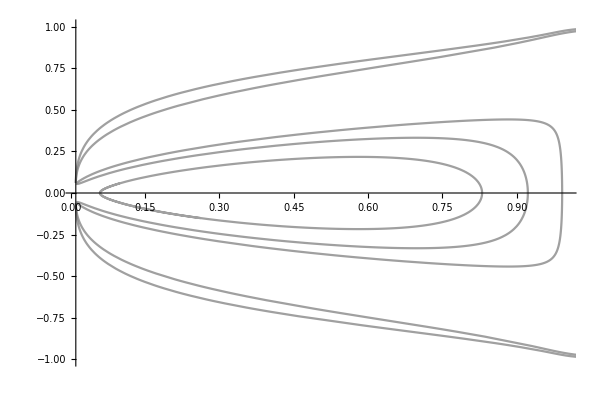

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],Y1[t]}/.sol[i],{i,1,10}], {t,-30,30},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,400},PlotRange->{{ℛ,1},{-1,1}}]]
```

```mathematica
traj[x0_,Y0_,Z0_]=NDSolve[{deX3Dt,deY3Dt,deZ3Dt, x1[0]==x0,Y1[0]==Y0,Z1[0]==Z0}, {x1,Y1,Z1},{t,-30,30}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.02,0,.001];
sol[2]=traj[0.02,0.01,.001];
sol[3]=traj[0.02,0.02,.001];
sol[4]=traj[0.02,0.3,.001];
sol[5]=traj[0.02,0.4,.001];
sol[6]=traj[0.02,.5,.001];
sol[7]=traj[0.02,.6,.001];
sol[8]=traj[0.02,.7,.001];
sol[9]=traj[0.02,.8,.001];
sol[10]=traj[0.02,.9,.001];
sol[11]=traj[0.98,0,.001];
```

NDSolve::ndsz: At t == -3.16285, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at t == -2.28462; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == -1.72907; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == -1.33195; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == -1.01958; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == -0.749761; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == -0.484253; unable to continue.

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

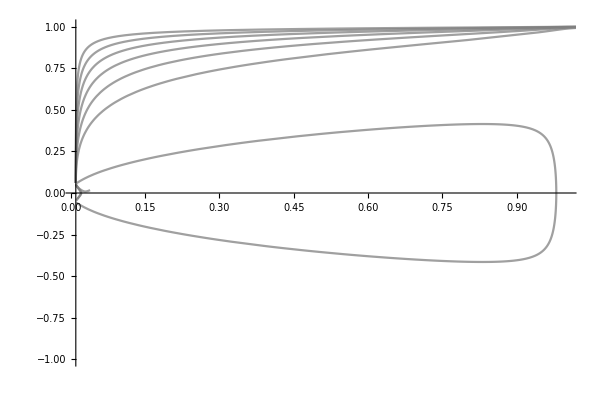

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],Y1[t]}/.sol[i],{i,1,11}], {t,-30,30},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,400},PlotRange->{{ℛ,1},{-1,1}}]]
```

## Ecological Models: Case 2

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z), Hubble parameter (y) and dark energy (x)*)
dex3D:=x'=-3*y*(x-ℛ)*(1-ϵ*x)-q*z*x*y
dez3D:=z'=-3*z*y + q*x*z*y
dey3D:=y'=-y^2-(1/6)*(x*(1+3*ϵ*ℛ)-3*ℛ-3*ϵ*x^2+z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex3D==0,dey3D==0,dez3D==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x+3 ℛ+3 x^2 ϵ-3 x ℛ ϵ},{x→3/q,y→-(√(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q-3 ϵ))/q^2},{x→3/q,y→(√(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q-3 ϵ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0},{x→1/ϵ,y→-1/(√3 √ϵ),z→0},{x→1/ϵ,y→1/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex3D,x],D[dex3D,y],D[dex3D,z]}, {D[dey3D,x],D[dey3D,y],D[dey3D,z]},{D[dez3D,x],D[dez3D,y],D[dez3D,z]}}];
J//MatrixForm
```

(-y (3+q z-6 x ϵ+3 ℛ ϵ) | -q x z+3 (x-ℛ) (-1+x ϵ) | -q x y
-1/6+x ϵ-(ℛ ϵ)/2 | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x+3 ℛ+3 x^2 ϵ-3 x ℛ ϵ) | (0 | 3 ℛ-3 q x^3 ϵ-3 x (1+q ℛ+ℛ ϵ)+x^2 (q+3 ϵ+3 q ℛ ϵ) | 0
-1/6+x ϵ-(ℛ ϵ)/2 | 0 | -1/6
0 | (-3+q x) (3 ℛ+3 x^2 ϵ-x (1+3 ℛ ϵ)) | 0) | (0
-(√(2 ℛ-4 x^2 ϵ+2 q x^3 ϵ+7 x ℛ ϵ-7 q x^2 ℛ ϵ-3 ℛ^2 ϵ+3 q x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)
(√(2 ℛ-4 x^2 ϵ+2 q x^3 ϵ+7 x ℛ ϵ-7 q x^2 ℛ ϵ-3 ℛ^2 ϵ+3 q x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)) | (-1/(1-6 x ϵ+3 ℛ ϵ) | 0 | 1
-(3 x-q x^2-3 ℛ+3 q x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (-x+3 ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | -(√(2 ℛ-4 x^2 ϵ+2 q x^3 ϵ+7 x ℛ ϵ-7 q x^2 ℛ ϵ-3 ℛ^2 ϵ+3 q x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (-x+3 ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1
-(3 x-q x^2-3 ℛ+3 q x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (-x+3 ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | (√(2 ℛ-4 x^2 ϵ+2 q x^3 ϵ+7 x ℛ ϵ-7 q x^2 ℛ ϵ-3 ℛ^2 ϵ+3 q x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (-x+3 ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1)
(3/q
-(√(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q-3 ϵ))/q^2) | (((q^2 ℛ-9 ϵ) √((q^2 ℛ)/3+3 ϵ-q ℛ ϵ))/q^2 | 0 | (√3 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/q
-1/6+(3 ϵ)/q-(ℛ ϵ)/2 | (2 √((q^2 ℛ)/3+3 ϵ-q ℛ ϵ))/q | -1/6
-((-3+q ℛ) (q-3 ϵ) √((q^2 ℛ)/3+3 ϵ-q ℛ ϵ))/q^2 | 0 | 0) | ((2 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/(√3 q)
(2 √3 q^2 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 √3 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-√(432 q^4 ℛ-144 q^5 ℛ^2+12 q^6 ℛ^3+3888 q^2 ϵ-3888 q^3 ℛ ϵ+756 q^4 ℛ^2 ϵ-36 q^5 ℛ^3 ϵ-11664 q ϵ^2+6804 q^2 ℛ ϵ^2-648 q^3 ℛ^2 ϵ^2+8748 ϵ^3-2916 q ℛ ϵ^3))/(12 q^2)
(2 √3 q^2 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 √3 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+√(432 q^4 ℛ-144 q^5 ℛ^2+12 q^6 ℛ^3+3888 q^2 ϵ-3888 q^3 ℛ ϵ+756 q^4 ℛ^2 ϵ-36 q^5 ℛ^3 ϵ-11664 q ϵ^2+6804 q^2 ℛ ϵ^2-648 q^3 ℛ^2 ϵ^2+8748 ϵ^3-2916 q ℛ ϵ^3))/(12 q^2)) | (0 | 1 | 0
(3 (-4 q^3 ℛ+q^4 ℛ^2-36 q ϵ+12 q^2 ℛ ϵ-3 q^3 ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))))/(2 (9 q^3 ℛ-2 q^4 ℛ^2+81 q ϵ-81 q^2 ℛ ϵ+15 q^3 ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))) | -(-6 q^3 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+q^4 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+99 q^2 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 q^3 ℛ ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+q^2 √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))/(-4 √3 q^3 ℛ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+√3 q^4 ℛ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+36 √3 q ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 √3 q^2 ℛ ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+81 √3 ϵ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-√3 (-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-4 √3 q √(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))) | 1
-(3 (-4 q^3 ℛ+q^4 ℛ^2-36 q ϵ+12 q^2 ℛ ϵ-3 q^3 ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))))/(2 (-9 q^3 ℛ+2 q^4 ℛ^2-81 q ϵ+81 q^2 ℛ ϵ-15 q^3 ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))) | -(-6 q^3 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+q^4 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+99 q^2 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 q^3 ℛ ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-q^2 √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))/(-4 √3 q^3 ℛ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+√3 q^4 ℛ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+36 √3 q ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 √3 q^2 ℛ ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+81 √3 ϵ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-√3 (-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+4 √3 q √(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))) | 1)
(3/q
(√(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q-3 ϵ))/q^2) | (((-q^2 ℛ+9 ϵ) √((q^2 ℛ)/3+3 ϵ-q ℛ ϵ))/q^2 | 0 | -(√3 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/q
-1/6+(3 ϵ)/q-(ℛ ϵ)/2 | -(2 √((q^2 ℛ)/3+3 ϵ-q ℛ ϵ))/q | -1/6
((-3+q ℛ) (q-3 ϵ) √((q^2 ℛ)/3+3 ϵ-q ℛ ϵ))/q^2 | 0 | 0) | (-(2 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ))/(√3 q)
(-2 √3 q^2 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+18 √3 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-√(432 q^4 ℛ-144 q^5 ℛ^2+12 q^6 ℛ^3+3888 q^2 ϵ-3888 q^3 ℛ ϵ+756 q^4 ℛ^2 ϵ-36 q^5 ℛ^3 ϵ-11664 q ϵ^2+6804 q^2 ℛ ϵ^2-648 q^3 ℛ^2 ϵ^2+8748 ϵ^3-2916 q ℛ ϵ^3))/(12 q^2)
(-2 √3 q^2 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+18 √3 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+√(432 q^4 ℛ-144 q^5 ℛ^2+12 q^6 ℛ^3+3888 q^2 ϵ-3888 q^3 ℛ ϵ+756 q^4 ℛ^2 ϵ-36 q^5 ℛ^3 ϵ-11664 q ϵ^2+6804 q^2 ℛ ϵ^2-648 q^3 ℛ^2 ϵ^2+8748 ϵ^3-2916 q ℛ ϵ^3))/(12 q^2)) | (0 | 1 | 0
-(3 (-4 q^3 ℛ+q^4 ℛ^2-36 q ϵ+12 q^2 ℛ ϵ-3 q^3 ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))))/(2 (-9 q^3 ℛ+2 q^4 ℛ^2-81 q ϵ+81 q^2 ℛ ϵ-15 q^3 ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))) | -(6 q^3 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-q^4 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-99 q^2 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+18 q^3 ℛ ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+q^2 √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))/(-4 √3 q^3 ℛ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+√3 q^4 ℛ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+36 √3 q ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 √3 q^2 ℛ ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+81 √3 ϵ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-√3 (-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+4 √3 q √(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))) | 1
(3 (-4 q^3 ℛ+q^4 ℛ^2-36 q ϵ+12 q^2 ℛ ϵ-3 q^3 ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))))/(2 (9 q^3 ℛ-2 q^4 ℛ^2+81 q ϵ-81 q^2 ℛ ϵ+15 q^3 ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))) | -(6 q^3 √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-q^4 ℛ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-99 q^2 ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)+18 q^3 ℛ ϵ √(q^2 ℛ+9 ϵ-3 q ℛ ϵ)-q^2 √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)))/(-4 √3 q^3 ℛ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+√3 q^4 ℛ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+36 √3 q ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-18 √3 q^2 ℛ ϵ (q^2 ℛ+9 ϵ-3 q ℛ ϵ)+81 √3 ϵ^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-√3 (-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ)-4 √3 q √(q^2 ℛ+9 ϵ-3 q ℛ ϵ) √((-6 q+q^2 ℛ+9 ϵ)^2 (q^2 ℛ+9 ϵ-3 q ℛ ϵ))) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (√3 √ℛ (1-ℛ ϵ) | 0 | (q ℛ^(3/2))/(√3)
1/6 (-1+3 ℛ ϵ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (3-q ℛ))/(√3)) | ((2 √ℛ)/(√3)
-(√ℛ (-3+q ℛ))/(√3)
-√3 √ℛ (-1+ℛ ϵ)) | (0 | 1 | 0
-q/(q-3 ϵ) | -(√3 ϵ)/(2 √ℛ (-q+3 ϵ)) | 1
-2 √3 √ℛ | 1 | 0)
(ℛ
(√ℛ)/(√3)
0) | (√3 √ℛ (-1+ℛ ϵ) | 0 | -(q ℛ^(3/2))/(√3)
1/6 (-1+3 ℛ ϵ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (-3+q ℛ))/(√3)) | (-(2 √ℛ)/(√3)
(√ℛ (-3+q ℛ))/(√3)
√3 √ℛ (-1+ℛ ϵ)) | (0 | 1 | 0
-q/(q-3 ϵ) | (√3 ϵ)/(2 √ℛ (-q+3 ϵ)) | 1
2 √3 √ℛ | 1 | 0)
(1/ϵ
-1/(√3 √ϵ)
0) | ((√3 (-1+ℛ ϵ))/(√ϵ) | 0 | q/(√3 ϵ^(3/2))
1/6 (5-3 ℛ ϵ) | 2/(√3 √ϵ) | -1/6
0 | 0 | (-q+3 ϵ)/(√3 ϵ^(3/2))) | (-(q-3 ϵ)/(√3 ϵ^(3/2))
2/(√3 √ϵ)
(√3 (-1+ℛ ϵ))/(√ϵ)) | (-q/(q-6 ϵ+3 ℛ ϵ^2) | -(√3 (-2 ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 (q-6 ϵ+3 ℛ ϵ^2)) | 1
0 | 1 | 0
-(2 √3)/(√ϵ) | 1 | 0)
(1/ϵ
1/(√3 √ϵ)
0) | ((√3 (1-ℛ ϵ))/(√ϵ) | 0 | -q/(√3 ϵ^(3/2))
1/6 (5-3 ℛ ϵ) | -2/(√3 √ϵ) | -1/6
0 | 0 | (q-3 ϵ)/(√3 ϵ^(3/2))) | ((q-3 ϵ)/(√3 ϵ^(3/2))
-2/(√3 √ϵ)
-(√3 (-1+ℛ ϵ))/(√ϵ)) | (-q/(q-6 ϵ+3 ℛ ϵ^2) | (√3 (-2 ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 (q-6 ϵ+3 ℛ ϵ^2)) | 1
0 | 1 | 0
(2 √3)/(√ϵ) | 1 | 0)

```mathematica
(*Define the differential equations in terms of their variables*)
DE23D[q_,ℛ_,ϵ_]=dex3D;
DM23D[q_]=dez3D;
H23D[q_,ℛ_,ϵ_]=dey3D;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot3D[{DE23D[q,ℛ,ϵ],H23D[q,ℛ,ϵ],DM23D[q]},{x,ℛ,1/ϵ},{y,-2,2},{z,0,2},AxesLabel->{"x","y","z"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"},{ ϵ,-3,3,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$8595'[System`VectorPlotsDump`t$8595]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8595[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$8595'[System`VectorPlotsDump`t$8595]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8595[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8595,System`VectorPlotsDump`linesxmax$8595},{System`VectorPlotsDump`linesymin$8595,System`VectorPlotsDump`linesymax$8595},{System`VectorPlotsDump`lineszmin$8595,«37»},{System`VectorPlotsDump`linesfieldmin$8595,System`VectorPlotsDump`linesfieldmax$8595}} and System`VectorPlotsDump`extremes$8657 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$8595'[System`VectorPlotsDump`t$8595]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8595[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$8595'[System`VectorPlotsDump`t$8595]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8595[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8595,System`VectorPlotsDump`linesxmax$8595},{System`VectorPlotsDump`linesymin$8595,System`VectorPlotsDump`linesymax$8595},{System`VectorPlotsDump`lineszmin$8595,«37»},{System`VectorPlotsDump`linesfieldmin$8595,System`VectorPlotsDump`linesfieldmax$8595}} and System`VectorPlotsDump`extremes$8733 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$8595'[System`VectorPlotsDump`t$8595]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8595[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$8595'[System`VectorPlotsDump`t$8595]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8595[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8595,System`VectorPlotsDump`linesxmax$8595},{System`VectorPlotsDump`linesymin$8595,System`VectorPlotsDump`linesymax$8595},{System`VectorPlotsDump`lineszmin$8595,«37»},{System`VectorPlotsDump`linesfieldmin$8595,System`VectorPlotsDump`linesfieldmax$8595}} and System`VectorPlotsDump`extremes$8815 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10066'[System`VectorPlotsDump`t$10066]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$10066[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$10066'[System`VectorPlotsDump`t$10066]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$10066[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10066,System`VectorPlotsDump`linesxmax$10066},{System`VectorPlotsDump`linesymin$10066,System`VectorPlotsDump`linesymax$10066},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10066,System`VectorPlotsDump`linesfieldmax$10066}} and System`VectorPlotsDump`extremes$10125 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10066'[System`VectorPlotsDump`t$10066]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$10066[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$10066'[System`VectorPlotsDump`t$10066]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$10066[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10066,System`VectorPlotsDump`linesxmax$10066},{System`VectorPlotsDump`linesymin$10066,System`VectorPlotsDump`linesymax$10066},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10066,System`VectorPlotsDump`linesfieldmax$10066}} and System`VectorPlotsDump`extremes$10191 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$10066'[System`VectorPlotsDump`t$10066]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$10066[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$10066'[System`VectorPlotsDump`t$10066]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$10066[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10066,System`VectorPlotsDump`linesxmax$10066},{System`VectorPlotsDump`linesymin$10066,System`VectorPlotsDump`linesymax$10066},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10066,System`VectorPlotsDump`linesfieldmax$10066}} and System`VectorPlotsDump`extremes$10265 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$8775'[System`VectorPlotsDump`t$8775]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8775[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$8775'[System`VectorPlotsDump`t$8775]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8775[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8775,System`VectorPlotsDump`linesxmax$8775},{System`VectorPlotsDump`linesymin$8775,System`VectorPlotsDump`linesymax$8775},{System`VectorPlotsDump`lineszmin$8775,«37»},{System`VectorPlotsDump`linesfieldmin$8775,System`VectorPlotsDump`linesfieldmax$8775}} and System`VectorPlotsDump`extremes$8840 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$8775'[System`VectorPlotsDump`t$8775]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8775[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$8775'[System`VectorPlotsDump`t$8775]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8775[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8775,System`VectorPlotsDump`linesxmax$8775},{System`VectorPlotsDump`linesymin$8775,System`VectorPlotsDump`linesymax$8775},{System`VectorPlotsDump`lineszmin$8775,«37»},{System`VectorPlotsDump`linesfieldmin$8775,System`VectorPlotsDump`linesfieldmax$8775}} and System`VectorPlotsDump`extremes$8915 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$8775'[System`VectorPlotsDump`t$8775]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8775[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$8775'[System`VectorPlotsDump`t$8775]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$8775[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Ext…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$8775,System`VectorPlotsDump`linesxmax$8775},{System`VectorPlotsDump`linesymin$8775,System`VectorPlotsDump`linesymax$8775},{System`VectorPlotsDump`lineszmin$8775,«37»},{System`VectorPlotsDump`linesfieldmin$8775,System`VectorPlotsDump`linesfieldmax$8775}} and System`VectorPlotsDump`extremes$9012 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12913'[System`VectorPlotsDump`t$12913]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$12913[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$12913'[System`VectorPlotsDump`t$12913]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$12913[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12913,System`VectorPlotsDump`linesxmax$12913},{System`VectorPlotsDump`linesymin$12913,System`VectorPlotsDump`linesymax$12913},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12913,System`VectorPlotsDump`linesfieldmax$12913}} and System`VectorPlotsDump`extremes$12970 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12913'[System`VectorPlotsDump`t$12913]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$12913[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$12913'[System`VectorPlotsDump`t$12913]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$12913[0]=={-0.3,-1.6,0.733333,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12913,System`VectorPlotsDump`linesxmax$12913},{System`VectorPlotsDump`linesymin$12913,System`VectorPlotsDump`linesymax$12913},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12913,System`VectorPlotsDump`linesfieldmax$12913}} and System`VectorPlotsDump`extremes$13036 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$12913'[System`VectorPlotsDump`t$12913]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$12913[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$12913'[System`VectorPlotsDump`t$12913]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$12913[0]=={-0.3,-1.6,1.26667,0.},WhenEvent[«1»,StopIntegration]},«30»,«1»,E…er→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$12913,System`VectorPlotsDump`linesxmax$12913},{System`VectorPlotsDump`linesymin$12913,System`VectorPlotsDump`linesymax$12913},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$12913,System`VectorPlotsDump`linesfieldmax$12913}} and System`VectorPlotsDump`extremes$13118 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$9516'[System`VectorPlotsDump`t$9516]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$9516[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$9516'[System`VectorPlotsDump`t$9516]=={DE23D[0,0,-3],H23D[0,0,-3],DM23D[0],√(DE23D[«3»]^2+DM23D[«1»]^2+H23D[«3»]^2)},System`VectorPlotsDump`w$9516[0]=={-0.3,-1.6,0.2,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$9516,System`VectorPlotsDump`linesxmax$9516},{System`VectorPlotsDump`linesymin$9516,System`VectorPlotsDump`linesymax$9516},{«37»,«37»},{System`VectorPlotsDump`linesfieldmin$9516,System`VectorPlotsDump`linesfieldmax$9516}} and System`VectorPlotsDump`extremes$9610 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$9516,System`VectorPlotsDump`linesxmax$9516},{System`VectorPlotsDump`linesymin$9516,System`VectorPlotsDump`linesymax$9516},{«37»,«37»},{System`VectorPlotsDump`linesfieldmin$9516,System`VectorPlotsDump`linesfieldmax$9516}} and System`VectorPlotsDump`extremes$9692 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$9516,System`VectorPlotsDump`linesxmax$9516},{System`VectorPlotsDump`linesymin$9516,System`VectorPlotsDump`linesymax$9516},{«37»,«37»},{System`VectorPlotsDump`linesfieldmin$9516,System`VectorPlotsDump`linesfieldmax$9516}} and System`VectorPlotsDump`extremes$9766 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*Define the dynamical system for coupled compact dark matter (Z), compact Hubble parameter (Y) and dark energy (x)*)
deX3D:=x'=-3*Y*(x-ℛ)*(1-ϵ*x)/((1-Y^2)^(1/2))-q*(Z/(1-Z))*x*(Y/((1-Y^2)^(1/2)))
deZ3D:=Z'=-3*(1-Z)*Z *Y/((1-Y^2)^(1/2))+ q*x*Z*(1-Z)*Y/((1-Y^2)^(1/2))
deY3D:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(x*(1+3*ϵ*ℛ)-3*ℛ-3*ϵ*x^2+Z/(1-Z))
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE23DCompact[q_,ℛ_,ϵ_]=deX3D;
DM23DCompact[q_]=deZ3D;
H23DCompact[q_,ℛ_,ϵ_]=deY3D;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot3D[{DE23DCompact[q,ℛ,ϵ],H23DCompact[q,ℛ,ϵ],DM23DCompact[q]},{x,ℛ,1/ϵ},{Y,-1,1},{Z,0,1},AxesLabel->{"x","Y","Z"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"},{ ϵ,-3,3,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$14158,System`VectorPlotsDump`linesxmax$14158},{System`VectorPlotsDump`linesymin$14158,System`VectorPlotsDump`linesymax$14158},{System`VectorPlotsDump`lineszmin$14158,«38»},{System`VectorPlotsDump`linesfieldmin$14158,System`VectorPlotsDump`linesfieldmax$14158}} and System`VectorPlotsDump`extremes$14244 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$14158,System`VectorPlotsDump`linesxmax$14158},{System`VectorPlotsDump`linesymin$14158,System`VectorPlotsDump`linesymax$14158},{System`VectorPlotsDump`lineszmin$14158,«38»},{System`VectorPlotsDump`linesfieldmin$14158,System`VectorPlotsDump`linesfieldmax$14158}} and System`VectorPlotsDump`extremes$14323 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$14158,System`VectorPlotsDump`linesxmax$14158},{System`VectorPlotsDump`linesymin$14158,System`VectorPlotsDump`linesymax$14158},{System`VectorPlotsDump`lineszmin$14158,«38»},{System`VectorPlotsDump`linesfieldmin$14158,System`VectorPlotsDump`linesfieldmax$14158}} and System`VectorPlotsDump`extremes$14384 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$15726,System`VectorPlotsDump`linesxmax$15726},{System`VectorPlotsDump`linesymin$15726,System`VectorPlotsDump`linesymax$15726},{System`VectorPlotsDump`lineszmin$15726,«38»},{System`VectorPlotsDump`linesfieldmin$15726,System`VectorPlotsDump`linesfieldmax$15726}} and System`VectorPlotsDump`extremes$15778 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$15726,System`VectorPlotsDump`linesxmax$15726},{System`VectorPlotsDump`linesymin$15726,System`VectorPlotsDump`linesymax$15726},{System`VectorPlotsDump`lineszmin$15726,«38»},{System`VectorPlotsDump`linesfieldmin$15726,System`VectorPlotsDump`linesfieldmax$15726}} and System`VectorPlotsDump`extremes$15833 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$15726,System`VectorPlotsDump`linesxmax$15726},{System`VectorPlotsDump`linesymin$15726,System`VectorPlotsDump`linesymax$15726},{System`VectorPlotsDump`lineszmin$15726,«38»},{System`VectorPlotsDump`linesfieldmin$15726,System`VectorPlotsDump`linesfieldmax$15726}} and System`VectorPlotsDump`extremes$15896 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11594,System`VectorPlotsDump`linesxmax$11594},{System`VectorPlotsDump`linesymin$11594,System`VectorPlotsDump`linesymax$11594},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11594,System`VectorPlotsDump`linesfieldmax$11594}} and System`VectorPlotsDump`extremes$11643 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11594,System`VectorPlotsDump`linesxmax$11594},{System`VectorPlotsDump`linesymin$11594,System`VectorPlotsDump`linesymax$11594},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11594,System`VectorPlotsDump`linesfieldmax$11594}} and System`VectorPlotsDump`extremes$11702 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11594,System`VectorPlotsDump`linesxmax$11594},{System`VectorPlotsDump`linesymin$11594,System`VectorPlotsDump`linesymax$11594},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11594,System`VectorPlotsDump`linesfieldmax$11594}} and System`VectorPlotsDump`extremes$11767 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10477,System`VectorPlotsDump`linesxmax$10477},{System`VectorPlotsDump`linesymin$10477,System`VectorPlotsDump`linesymax$10477},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10477,System`VectorPlotsDump`linesfieldmax$10477}} and System`VectorPlotsDump`extremes$10524 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10477,System`VectorPlotsDump`linesxmax$10477},{System`VectorPlotsDump`linesymin$10477,System`VectorPlotsDump`linesymax$10477},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10477,System`VectorPlotsDump`linesfieldmax$10477}} and System`VectorPlotsDump`extremes$10579 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$10477,System`VectorPlotsDump`linesxmax$10477},{System`VectorPlotsDump`linesymin$10477,System`VectorPlotsDump`linesymax$10477},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$10477,System`VectorPlotsDump`linesfieldmax$10477}} and System`VectorPlotsDump`extremes$10644 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$14578,System`VectorPlotsDump`linesxmax$14578},{System`VectorPlotsDump`linesymin$14578,System`VectorPlotsDump`linesymax$14578},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$14578,System`VectorPlotsDump`linesfieldmax$14578}} and System`VectorPlotsDump`extremes$14631 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$14578,System`VectorPlotsDump`linesxmax$14578},{System`VectorPlotsDump`linesymin$14578,System`VectorPlotsDump`linesymax$14578},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$14578,System`VectorPlotsDump`linesfieldmax$14578}} and System`VectorPlotsDump`extremes$14688 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$14578,System`VectorPlotsDump`linesxmax$14578},{System`VectorPlotsDump`linesymin$14578,System`VectorPlotsDump`linesymax$14578},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$14578,System`VectorPlotsDump`linesfieldmax$14578}} and System`VectorPlotsDump`extremes$14747 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11112,System`VectorPlotsDump`linesxmax$11112},{System`VectorPlotsDump`linesymin$11112,System`VectorPlotsDump`linesymax$11112},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11112,System`VectorPlotsDump`linesfieldmax$11112}} and System`VectorPlotsDump`extremes$11167 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11112'[System`VectorPlotsDump`t$11112]==«1»,System`VectorPlotsDump`w$11112[0]=={0.109,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$11112,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11112'[System`VectorPlotsDump`t$11112]==«1»,System`VectorPlotsDump`w$11112[0]=={0.109,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$11112,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11112,System`VectorPlotsDump`linesxmax$11112},{System`VectorPlotsDump`linesymin$11112,System`VectorPlotsDump`linesymax$11112},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11112,System`VectorPlotsDump`linesfieldmax$11112}} and System`VectorPlotsDump`extremes$11235 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$11112'[System`VectorPlotsDump`t$11112]==«1»,System`VectorPlotsDump`w$11112[0]=={0.109,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$11112,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$11112'[System`VectorPlotsDump`t$11112]==«1»,System`VectorPlotsDump`w$11112[0]=={0.109,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$11112,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$11112,System`VectorPlotsDump`linesxmax$11112},{System`VectorPlotsDump`linesymin$11112,System`VectorPlotsDump`linesymax$11112},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$11112,System`VectorPlotsDump`linesfieldmax$11112}} and System`VectorPlotsDump`extremes$11311 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$19853,System`VectorPlotsDump`linesxmax$19853},{System`VectorPlotsDump`linesymin$19853,System`VectorPlotsDump`linesymax$19853},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$19853,System`VectorPlotsDump`linesfieldmax$19853}} and System`VectorPlotsDump`extremes$19907 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$19853'[System`VectorPlotsDump`t$19853]==«1»,System`VectorPlotsDump`w$19853[0]=={0.109,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$19853,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$19853'[System`VectorPlotsDump`t$19853]==«1»,System`VectorPlotsDump`w$19853[0]=={0.109,-0.8,0.366667,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$19853,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$19853,System`VectorPlotsDump`linesxmax$19853},{System`VectorPlotsDump`linesymin$19853,System`VectorPlotsDump`linesymax$19853},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$19853,System`VectorPlotsDump`linesfieldmax$19853}} and System`VectorPlotsDump`extremes$19975 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$19853'[System`VectorPlotsDump`t$19853]==«1»,System`VectorPlotsDump`w$19853[0]=={0.109,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$19853,«1»,Ex…ler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$19853'[System`VectorPlotsDump`t$19853]==«1»,System`VectorPlotsDump`w$19853[0]=={0.109,-0.8,0.633333,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$19853,«1»,Ex…ler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$19853,System`VectorPlotsDump`linesxmax$19853},{System`VectorPlotsDump`linesymin$19853,System`VectorPlotsDump`linesymax$19853},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$19853,System`VectorPlotsDump`linesfieldmax$19853}} and System`VectorPlotsDump`extremes$20049 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*(x-ℛ)*(1-ϵ*x)-q*z*x
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→((-3+q ℛ) (q-3 ϵ))/q^2},{x→ℛ,z→0},{x→1/ϵ,z→0}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-q z+6 x ϵ-3 ℛ ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
((-3+q ℛ) (q-3 ϵ))/q^2) | (-q ℛ+(9 ϵ)/q | -3
((-3+q ℛ) (q-3 ϵ))/q | 0) | ((3 q-q^2 ℛ)/q
-(3 (q-3 ϵ))/q) | (-q/(q-3 ϵ) | 1
-3/(-3+q ℛ) | 1)
(ℛ
0) | (-3+3 ℛ ϵ | -q ℛ
0 | -3+q ℛ) | (-3+q ℛ
3 (-1+ℛ ϵ)) | (-q/(q-3 ϵ) | 1
1 | 0)
(1/ϵ
0) | (3-3 ℛ ϵ | -q/ϵ
0 | -3+q/ϵ) | ((q-3 ϵ)/ϵ
-3 (-1+ℛ ϵ)) | (-q/(q-6 ϵ+3 ℛ ϵ^2) | 1
1 | 0)

```mathematica
(*Define the differential equations in terms of their variables*)
DE2[q_,ℛ_,ϵ_]=dex;
DM2[q_]=dez;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot[{DM2[q],DE2[q,ℛ,ϵ]},{z,0,2},{x,ℛ,1/ϵ},FrameLabel->{"z","x"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"},{ ϵ,-1,1,Appearance->"Open"}]
```

```mathematica
(*Define differential equations for dark energy (x) and compact dark matter (Z)*)
deX:=x'=-3*(x-ℛ)*(1-ϵ*x)-q*Z*x/(1-Z)
deZ:=Z'=-3*(1-Z)*Z + q*x*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{x,Z}]
```

{{x→3/q,Z→((-3+q ℛ) (q-3 ϵ))/(-3 q+q^2+q^2 ℛ+9 ϵ-3 q ℛ ϵ)},{x→ℛ,Z→0},{x→1/ϵ,Z→0}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,x],D[deX,Z]}, {D[deZ,x],D[deZ,Z]}}];
J//MatrixForm
```

(-3+(q Z)/(-1+Z)+6 x ϵ-3 ℛ ϵ | -(q x)/(-1+Z)^2
-q (-1+Z) Z | -((-3+q x) (-1+2 Z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
z) | (-3+(q z)/(-1+z)+(18 ϵ)/q-3 ℛ ϵ | -3/(-1+z)^2
-q (-1+z) z | 0) | ((-3 q+6 q z-q^2 z-3 q z^2+q^2 z^2+18 ϵ-36 z ϵ+18 z^2 ϵ-3 q ℛ ϵ+6 q z ℛ ϵ-3 q z^2 ℛ ϵ-√(-4 (3 q^3 z-9 q^3 z^2+9 q^3 z^3-3 q^3 z^4)+(3 q-6 q z+q^2 z+3 q z^2-q^2 z^2-18 ϵ+36 z ϵ-18 z^2 ϵ+3 q ℛ ϵ-6 q z ℛ ϵ+3 q z^2 ℛ ϵ)^2))/(2 q (-1+z)^2)
(-3 q+6 q z-q^2 z-3 q z^2+q^2 z^2+18 ϵ-36 z ϵ+18 z^2 ϵ-3 q ℛ ϵ+6 q z ℛ ϵ-3 q z^2 ℛ ϵ+√(-4 (3 q^3 z-9 q^3 z^2+9 q^3 z^3-3 q^3 z^4)+(3 q-6 q z+q^2 z+3 q z^2-q^2 z^2-18 ϵ+36 z ϵ-18 z^2 ϵ+3 q ℛ ϵ-6 q z ℛ ϵ+3 q z^2 ℛ ϵ)^2))/(2 q (-1+z)^2)) | (-(3 q-6 q z+q^2 z+3 q z^2-q^2 z^2-18 ϵ+36 z ϵ-18 z^2 ϵ+3 q ℛ ϵ-6 q z ℛ ϵ+3 q z^2 ℛ ϵ+√((-1+z)^2 (9 q^2-18 q^2 z-6 q^3 z+9 q^2 z^2+6 q^3 z^2+q^4 z^2-108 q ϵ+216 q z ϵ-36 q^2 z ϵ-108 q z^2 ϵ+36 q^2 z^2 ϵ+18 q^2 ℛ ϵ-36 q^2 z ℛ ϵ+6 q^3 z ℛ ϵ+18 q^2 z^2 ℛ ϵ-6 q^3 z^2 ℛ ϵ+324 ϵ^2-648 z ϵ^2+324 z^2 ϵ^2-108 q ℛ ϵ^2+216 q z ℛ ϵ^2-108 q z^2 ℛ ϵ^2+9 q^2 ℛ^2 ϵ^2-18 q^2 z ℛ^2 ϵ^2+9 q^2 z^2 ℛ^2 ϵ^2)))/(2 q^2 z-6 q^2 z^2+6 q^2 z^3-2 q^2 z^4) | 1
-(3 q-6 q z+q^2 z+3 q z^2-q^2 z^2-18 ϵ+36 z ϵ-18 z^2 ϵ+3 q ℛ ϵ-6 q z ℛ ϵ+3 q z^2 ℛ ϵ-√((-1+z)^2 (9 q^2-18 q^2 z-6 q^3 z+9 q^2 z^2+6 q^3 z^2+q^4 z^2-108 q ϵ+216 q z ϵ-36 q^2 z ϵ-108 q z^2 ϵ+36 q^2 z^2 ϵ+18 q^2 ℛ ϵ-36 q^2 z ℛ ϵ+6 q^3 z ℛ ϵ+18 q^2 z^2 ℛ ϵ-6 q^3 z^2 ℛ ϵ+324 ϵ^2-648 z ϵ^2+324 z^2 ϵ^2-108 q ℛ ϵ^2+216 q z ℛ ϵ^2-108 q z^2 ℛ ϵ^2+9 q^2 ℛ^2 ϵ^2-18 q^2 z ℛ^2 ϵ^2+9 q^2 z^2 ℛ^2 ϵ^2)))/(2 q^2 z-6 q^2 z^2+6 q^2 z^3-2 q^2 z^4) | 1)
(ℛ
z) | (-3+(q z)/(-1+z)+3 ℛ ϵ | -(q ℛ)/(-1+z)^2
-q (-1+z) z | -((-1+2 z) (-3+q ℛ))) | ((-6+18 z-q z-18 z^2+q z^2+6 z^3+q ℛ-4 q z ℛ+5 q z^2 ℛ-2 q z^3 ℛ+3 ℛ ϵ-6 z ℛ ϵ+3 z^2 ℛ ϵ-(-1+z) √(36 z^2+12 q z^2+q^2 z^2-72 z^3-12 q z^3+36 z^4+12 q z ℛ-2 q^2 z ℛ-48 q z^2 ℛ-2 q^2 z^2 ℛ+60 q z^3 ℛ+4 q^2 z^3 ℛ-24 q z^4 ℛ+q^2 ℛ^2-6 q^2 z ℛ^2+13 q^2 z^2 ℛ^2-12 q^2 z^3 ℛ^2+4 q^2 z^4 ℛ^2-36 z ℛ ϵ-6 q z ℛ ϵ+72 z^2 ℛ ϵ+6 q z^2 ℛ ϵ-36 z^3 ℛ ϵ-6 q ℛ^2 ϵ+24 q z ℛ^2 ϵ-30 q z^2 ℛ^2 ϵ+12 q z^3 ℛ^2 ϵ+9 ℛ^2 ϵ^2-18 z ℛ^2 ϵ^2+9 z^2 ℛ^2 ϵ^2))/(2 (-1+z)^2)
(-6+18 z-q z-18 z^2+q z^2+6 z^3+q ℛ-4 q z ℛ+5 q z^2 ℛ-2 q z^3 ℛ+3 ℛ ϵ-6 z ℛ ϵ+3 z^2 ℛ ϵ+(-1+z) √(36 z^2+12 q z^2+q^2 z^2-72 z^3-12 q z^3+36 z^4+12 q z ℛ-2 q^2 z ℛ-48 q z^2 ℛ-2 q^2 z^2 ℛ+60 q z^3 ℛ+4 q^2 z^3 ℛ-24 q z^4 ℛ+q^2 ℛ^2-6 q^2 z ℛ^2+13 q^2 z^2 ℛ^2-12 q^2 z^3 ℛ^2+4 q^2 z^4 ℛ^2-36 z ℛ ϵ-6 q z ℛ ϵ+72 z^2 ℛ ϵ+6 q z^2 ℛ ϵ-36 z^3 ℛ ϵ-6 q ℛ^2 ϵ+24 q z ℛ^2 ϵ-30 q z^2 ℛ^2 ϵ+12 q z^3 ℛ^2 ϵ+9 ℛ^2 ϵ^2-18 z ℛ^2 ϵ^2+9 z^2 ℛ^2 ϵ^2))/(2 (-1+z)^2)) | (-(6 z+q z-6 z^2+q ℛ-3 q z ℛ+2 q z^2 ℛ-3 ℛ ϵ+3 z ℛ ϵ-√(36 z^2+12 q z^2+q^2 z^2-72 z^3-12 q z^3+36 z^4+12 q z ℛ-2 q^2 z ℛ-48 q z^2 ℛ-2 q^2 z^2 ℛ+60 q z^3 ℛ+4 q^2 z^3 ℛ-24 q z^4 ℛ+q^2 ℛ^2-6 q^2 z ℛ^2+13 q^2 z^2 ℛ^2-12 q^2 z^3 ℛ^2+4 q^2 z^4 ℛ^2-36 z ℛ ϵ-6 q z ℛ ϵ+72 z^2 ℛ ϵ+6 q z^2 ℛ ϵ-36 z^3 ℛ ϵ-6 q ℛ^2 ϵ+24 q z ℛ^2 ϵ-30 q z^2 ℛ^2 ϵ+12 q z^3 ℛ^2 ϵ+9 ℛ^2 ϵ^2-18 z ℛ^2 ϵ^2+9 z^2 ℛ^2 ϵ^2))/(2 q (-1+z)^2 z) | 1
-(6 z+q z-6 z^2+q ℛ-3 q z ℛ+2 q z^2 ℛ-3 ℛ ϵ+3 z ℛ ϵ+√(36 z^2+12 q z^2+q^2 z^2-72 z^3-12 q z^3+36 z^4+12 q z ℛ-2 q^2 z ℛ-48 q z^2 ℛ-2 q^2 z^2 ℛ+60 q z^3 ℛ+4 q^2 z^3 ℛ-24 q z^4 ℛ+q^2 ℛ^2-6 q^2 z ℛ^2+13 q^2 z^2 ℛ^2-12 q^2 z^3 ℛ^2+4 q^2 z^4 ℛ^2-36 z ℛ ϵ-6 q z ℛ ϵ+72 z^2 ℛ ϵ+6 q z^2 ℛ ϵ-36 z^3 ℛ ϵ-6 q ℛ^2 ϵ+24 q z ℛ^2 ϵ-30 q z^2 ℛ^2 ϵ+12 q z^3 ℛ^2 ϵ+9 ℛ^2 ϵ^2-18 z ℛ^2 ϵ^2+9 z^2 ℛ^2 ϵ^2))/(2 q (-1+z)^2 z) | 1)
(1/ϵ
z) | (3+(q z)/(-1+z)-3 ℛ ϵ | -q/((-1+z)^2 ϵ)
-q (-1+z) z | -((-1+2 z) (-3+q/ϵ))) | ((q-4 q z+5 q z^2-2 q z^3+6 z ϵ-q z ϵ-12 z^2 ϵ+q z^2 ϵ+6 z^3 ϵ-3 ℛ ϵ^2+6 z ℛ ϵ^2-3 z^2 ℛ ϵ^2-(-1+z) √(q^2-6 q^2 z+13 q^2 z^2-12 q^2 z^3+4 q^2 z^4-12 q ϵ+60 q z ϵ-2 q^2 z ϵ-108 q z^2 ϵ-2 q^2 z^2 ϵ+84 q z^3 ϵ+4 q^2 z^3 ϵ-24 q z^4 ϵ+36 ϵ^2-144 z ϵ^2-12 q z ϵ^2+216 z^2 ϵ^2+24 q z^2 ϵ^2+q^2 z^2 ϵ^2-144 z^3 ϵ^2-12 q z^3 ϵ^2+36 z^4 ϵ^2+6 q ℛ ϵ^2-24 q z ℛ ϵ^2+30 q z^2 ℛ ϵ^2-12 q z^3 ℛ ϵ^2-36 ℛ ϵ^3+108 z ℛ ϵ^3+6 q z ℛ ϵ^3-108 z^2 ℛ ϵ^3-6 q z^2 ℛ ϵ^3+36 z^3 ℛ ϵ^3+9 ℛ^2 ϵ^4-18 z ℛ^2 ϵ^4+9 z^2 ℛ^2 ϵ^4))/(2 (-1+z)^2 ϵ)
(q-4 q z+5 q z^2-2 q z^3+6 z ϵ-q z ϵ-12 z^2 ϵ+q z^2 ϵ+6 z^3 ϵ-3 ℛ ϵ^2+6 z ℛ ϵ^2-3 z^2 ℛ ϵ^2+(-1+z) √(q^2-6 q^2 z+13 q^2 z^2-12 q^2 z^3+4 q^2 z^4-12 q ϵ+60 q z ϵ-2 q^2 z ϵ-108 q z^2 ϵ-2 q^2 z^2 ϵ+84 q z^3 ϵ+4 q^2 z^3 ϵ-24 q z^4 ϵ+36 ϵ^2-144 z ϵ^2-12 q z ϵ^2+216 z^2 ϵ^2+24 q z^2 ϵ^2+q^2 z^2 ϵ^2-144 z^3 ϵ^2-12 q z^3 ϵ^2+36 z^4 ϵ^2+6 q ℛ ϵ^2-24 q z ℛ ϵ^2+30 q z^2 ℛ ϵ^2-12 q z^3 ℛ ϵ^2-36 ℛ ϵ^3+108 z ℛ ϵ^3+6 q z ℛ ϵ^3-108 z^2 ℛ ϵ^3-6 q z^2 ℛ ϵ^3+36 z^3 ℛ ϵ^3+9 ℛ^2 ϵ^4-18 z ℛ^2 ϵ^4+9 z^2 ℛ^2 ϵ^4))/(2 (-1+z)^2 ϵ)) | (-(q-3 q z+2 q z^2-6 ϵ+12 z ϵ+q z ϵ-6 z^2 ϵ+3 ℛ ϵ^2-3 z ℛ ϵ^2-√(q^2-6 q^2 z+13 q^2 z^2-12 q^2 z^3+4 q^2 z^4-12 q ϵ+60 q z ϵ-2 q^2 z ϵ-108 q z^2 ϵ-2 q^2 z^2 ϵ+84 q z^3 ϵ+4 q^2 z^3 ϵ-24 q z^4 ϵ+36 ϵ^2-144 z ϵ^2-12 q z ϵ^2+216 z^2 ϵ^2+24 q z^2 ϵ^2+q^2 z^2 ϵ^2-144 z^3 ϵ^2-12 q z^3 ϵ^2+36 z^4 ϵ^2+6 q ℛ ϵ^2-24 q z ℛ ϵ^2+30 q z^2 ℛ ϵ^2-12 q z^3 ℛ ϵ^2-36 ℛ ϵ^3+108 z ℛ ϵ^3+6 q z ℛ ϵ^3-108 z^2 ℛ ϵ^3-6 q z^2 ℛ ϵ^3+36 z^3 ℛ ϵ^3+9 ℛ^2 ϵ^4-18 z ℛ^2 ϵ^4+9 z^2 ℛ^2 ϵ^4))/(2 q (-1+z)^2 z ϵ) | 1
-(q-3 q z+2 q z^2-6 ϵ+12 z ϵ+q z ϵ-6 z^2 ϵ+3 ℛ ϵ^2-3 z ℛ ϵ^2+√(q^2-6 q^2 z+13 q^2 z^2-12 q^2 z^3+4 q^2 z^4-12 q ϵ+60 q z ϵ-2 q^2 z ϵ-108 q z^2 ϵ-2 q^2 z^2 ϵ+84 q z^3 ϵ+4 q^2 z^3 ϵ-24 q z^4 ϵ+36 ϵ^2-144 z ϵ^2-12 q z ϵ^2+216 z^2 ϵ^2+24 q z^2 ϵ^2+q^2 z^2 ϵ^2-144 z^3 ϵ^2-12 q z^3 ϵ^2+36 z^4 ϵ^2+6 q ℛ ϵ^2-24 q z ℛ ϵ^2+30 q z^2 ℛ ϵ^2-12 q z^3 ℛ ϵ^2-36 ℛ ϵ^3+108 z ℛ ϵ^3+6 q z ℛ ϵ^3-108 z^2 ℛ ϵ^3-6 q z^2 ℛ ϵ^3+36 z^3 ℛ ϵ^3+9 ℛ^2 ϵ^4-18 z ℛ^2 ϵ^4+9 z^2 ℛ^2 ϵ^4))/(2 q (-1+z)^2 z ϵ) | 1)

```mathematica
(*Define the differential equations in terms of their variables*)
DE2Compact[q_,ℛ_,ϵ_]=deX;
DM2Compact[q_]=deZ;
```

```mathematica
(*Plot the phase space for the system*)
Manipulate[StreamPlot[{DM2Compact[q],DE2Compact[q,ℛ,ϵ]},{Z,0,1},{x,ℛ,1/ϵ},FrameLabel->{"Z","x"}],{q,0,20,Appearance->"Open"},{ ℛ,0,0.1,Appearance->"Open"},{ ϵ,-1,1,Appearance->"Open"}]
```

### Numeric Integration

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
q=0.01;
ℛ=0.01;
ϵ=0.01;
```

```mathematica
(*Define the dynamical system for coupled compact dark matter (Z), compact Hubble parameter (Y) and dark energy (x)*)
deX3Dt2:=x1'[t]==-3*Y1[t]*(x1[t]-ℛ)*(1-ϵ*x1[t])/((1-Y1[t]^2)^(1/2))-q*(Z1[t]/(1-Z1[t]))*x1[t]*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deZ3Dt2:=Z1'[t]==-3*(1-Z1[t])*Z1[t]*Y1[t]/((1-Y1[t]^2)^(1/2))+ q*x1[t]*Z1[t]*(1-Z1[t])*Y1[t]/((1-Y1[t]^2)^(1/2))
deY3Dt2:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*(x1[t]*(1+3*ϵ*ℛ)-3*ℛ-3*ϵ*x1[t]^2+Z1[t]/(1-Z1[t]))
```

```mathematica
traj[x0_,Y0_,Z0_]=NDSolve[{deX3Dt2,deY3Dt2,deZ3Dt2, x1[0]==x0,Y1[0]==Y0,Z1[0]==Z0}, {x1,Y1,Z1},{t,-30,30}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.6,0.8,0.2];
sol[2]=traj[0.7,0.2,0.2];
sol[3]=traj[0.7,0.5,0.5];
sol[4]=traj[0.9,0.2,0.1];
sol[5]=traj[0.5,0.7,0.3];
sol[6]=traj[0.99,0.2,0.01];
sol[7]=traj[0.6,-0.8,0.2];
sol[8]=traj[0.7,-0.5,0.5];
sol[9]=traj[0.5,-0.7,0.3];
sol[10]=traj[0.9,0.1,0.8];
```

NDSolve::ndcf: Repeated convergence test failure at t == -0.729664; unable to continue.

NDSolve::ndsz: At t == -1.27701, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at t == -0.927919; unable to continue.

NDSolve::ndcf: Repeated convergence test failure at t == 0.729724; unable to continue.

NDSolve::ndsz: At t == 1.27701, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndcf: Repeated convergence test failure at t == 0.927917; unable to continue.

NDSolve::ndsz: At t == -1.41708, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mxst: Maximum number of 646095 steps reached at the point t == 4.25102.

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],Y1[t]}/.sol[i],{i,1,10}], {t,-30,30},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,400},PlotRange->{{ℛ,1},{-1,1}}]]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-